## Utilities

```mathematica
myNorm[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]
myNormMass[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2+1]
MS[v_]:=v[[1]]^2-v[[2]]^2-v[[3]]^2-v[[4]]^2
Get["/Users/zeno/cLTD-main/cLTD.m"]
Options[cLTD]
SetOptions[cLTD,"FORMpath"->"/usr/local/bin/form"]
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

{loopmom→{k0,k1,k2,k3},FORMpath→form,tFORMpath→tform,WorkingDirectory→/Users/zeno/Documents/,FORM_ID→None,FORMcores→1,OptimizationLVL→0,keep_FORM_script→False,EvalAll→False,NoNumerator→False,FORMsubs→False}

{loopmom→{k0,k1,k2,k3},FORMpath→/usr/local/bin/form,tFORMpath→tform,WorkingDirectory→/Users/zeno/Documents/,FORM_ID→None,FORMcores→1,OptimizationLVL→0,keep_FORM_script→False,EvalAll→False,NoNumerator→False,FORMsubs→False}

## -Graphics-

## -Graphics-

```mathematica
props1=prop[k,0]*prop[k-l,0]*prop[l,0]*prop[l-m,0]*prop[l+q,0]*prop[k+q,0]
diag1=cLTD[props1,loopmom->{k,l},EvalAll->True];
CForm[diag1[[1]]]
diag1[[2]]
integrand1[ks_,ls_,ms_,ns_]:=diag1[[1]]/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[l,0] prop[l-m,0] prop[k+q,0] prop[l+q,0]

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q)}

-0.015625*(1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E2 + E4 - q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) + 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) + 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E2 + E3 - m(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E2 + E4 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) + 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) + 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E0 + E4 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E1 + E4 + E5)*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E2 + E3 + m(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E1 + E2)*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) + 
      1/((E0 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))))/(E0*E1*E2*E3*E4*E5)

```mathematica
N[integrand1[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

6.20329278986×10^-9

### CounterTerms

#### Threshold 1

-Graphics-

Two-loop CounterTerm

```mathematica
ct1LTD=-(1/(64 E0 E1 E2 E3 E4 E5))(1/((E1+E4+E5) (E2+E3+m[0]) (E1+E2+E4-q[0]))+1/((E0+E1+E2) (E0+E1+E3+m[0])  (E0+E1+E5-q[0]))+1/((E0+E1+E3+m[0]) (E2+E3+m[0])  (E0+E1+E5-q[0]))+1/((E2+E3+m[0]) (E1+E2+E4-q[0]) (E2+E5-q[0]))+1/((E2+E3+m[0]) (E0+E1+E5-q[0]) (E2+E5-q[0]))+1/((E1+E4+E5) (E2+E3-m[0]) (E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))+1/( (E1+E2+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2) (E2+E3-m[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E2)(E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E5-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))+1/((E2+E3-m[0])(E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))+1/((E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))+1/((E0+E1+E2) (E2+E3-m[0])(E2+E5+q[0]))+1/((E1+E4+E5) (E2+E3-m[0]) (E2+E5+q[0]))+1/((E0+E1+E2) (E0+E1+E3+m[0]) (E3+E5+m[0]+q[0]))+1/((E1+E4+E5) (E2+E3+m[0]) (E3+E5+m[0]+q[0]))+1/((E0+E1+E3+m[0]) (E2+E3+m[0])(E3+E5+m[0]+q[0]))+1/((E0+E1+E2)(E2+E5+q[0]) (E3+E5+m[0]+q[0]))+1/((E1+E4+E5) (E2+E5+q[0]) (E3+E5+m[0]+q[0])));
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q)}

```mathematica
ct1integrand1[ks_,ls_,ms_,ns_]:=ct1LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT12L[ks_,ls_,ms_,ns_]:=((1/(2myNorm[ks]Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct1integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2myNorm[ks])]}
```

```mathematica
N[fullCT12L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

1.50823563979×10^-9

Series::ztest1: Unable to decide whether numeric quantity 1/2 Log[1+(1+1/2 Power[«2»])^2]-Log[Root[73-88 Power[«2»]+16 Power[«2»]&,4,0]] is equal to zero. Assuming it is.

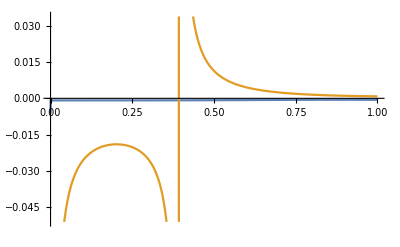

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}];
Series[fullCT12L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}];

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT12L[kt,lt,mt+eps{1,1,0},nt],integrand1[kt,lt,mt+eps{1,1,0},nt]},{eps,0,1}]
```

One-loop CounterTerm

```mathematica
fullCT11L[ks_,ls_,ms_,ns_]:=((1/(2Exp[r](Log[myNorm[ks]]-r))*ct1integrand1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])/2]}
```

```mathematica
N[fullCT11L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

5.44885556633×10^-9

(2 √(2/(11+4 √3)) (-436-277 √2+20 √3+28 √6-152 √(11+4 √3)-118 √(2 (11+4 √3))+46 √(3 (11+4 √3))+24 √(6 (11+4 √3))))/((2+√2) (√2-√3) (2+√3)^2 (4+√3) (2+√2+√3) (√3-√(11+4 √3)) (2 √2-√3+√(11+4 √3)) (4+√3+√(11+4 √3)) (2 √2+√3+√(11+4 √3)) eps)+O[eps]^0

Series::ztest1: Unable to decide whether numeric quantity Log[2]+Log[1+(√3)/2]-Log[2+√3] is equal to zero. Assuming it is.

-(2 (√(2/(3 (11+4 √3))) (-60-84 √2+436 √3+277 √6-138 √(11+4 √3)-72 √(2 (11+4 √3))+152 √(3 (11+4 √3))+118 √(6 (11+4 √3)))))/(((2+√2) (√2-√3) (2+√3)^2 (4+√3) (2+√2+√3) (√3-√(11+4 √3)) (2 √2-√3+√(11+4 √3)) (4+√3+√(11+4 √3)) (2 √2+√3+√(11+4 √3))) eps)+O[eps]^0

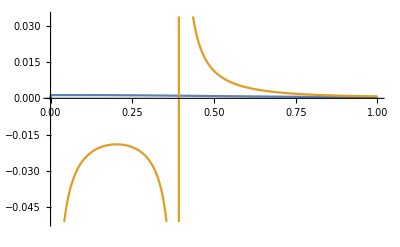

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT11L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT11L[kt,lt,mt+eps{1,1,0},nt],integrand1[kt,lt,mt+eps{1,1,0},nt]},{eps,0,1}]
```

#### Threshold 2

-Graphics-

```mathematica
ct2LTD=-(1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E2+E4-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E1+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))+1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5)*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E3+m[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E4+q[0]))+1/((E0+E1+E2)*(E3+E5-m[0]-q[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E3+E5-m[0]-q[0])*(E0+E4+q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E2+E3+m[0]) (E1+E2+E4-q[0]))-1/((E2+E3+m[0]) (E0+E4-q[0]) (E1+E2+E4-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E1+E5-q[0]))-1/((E2+E3+m[0]) (E0+E4-q[0]) (E0+E1+E5-q[0]))-1/((E0+E1+E2) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E1+E2+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5) (E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E0+E1+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E2+E3+m[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E4+q[0]))-1/((E0+E1+E2) (E3+E5-m[0]-q[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E3+E5-m[0]-q[0]) (E0+E4+q[0])))

```mathematica
ct2integrand1[ks_,ls_,ms_,ns_]:=ct2LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT22L[ks_,ls_,ms_,ns_]:=((1/(2myNorm[ls]Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct2integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2myNorm[ls])]}
```

```mathematica
N[fullCT22L[{1,2,3},{4,5,6},{3,2,2},{1,1,1}],12]
```

0.0000357754535715

(16 (11+4 √3+4 √(11+4 √3)))/((2+√3)^2 (4+√3) √(169+88 √3) (√3-√(11+4 √3))^2 (√3+√(11+4 √3)) (4+√3+√(11+4 √3)) eps)+O[eps]^0

Series::ztest1: Unable to decide whether numeric quantity 1/2 Log[1+(1+1/2 Power[«2»])^2]-Log[Root[73-88 Power[«2»]+16 Power[«2»]&,4,0]] is equal to zero. Assuming it is.

(32 (12+11 √3+4 √(3 (11+4 √3))) Root2.12Root[73-88 #1^2+16 #1^4&,4]2.117085451173116)/(√3 (2+√3)^2 (4+√3) (11+4 √3)^(3/2) (√3-√(11+4 √3))^2 (√3+√(11+4 √3)) (4+√3+√(11+4 √3)) eps)+O[eps]^0

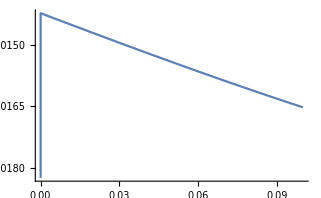

```mathematica
kt={0,1,0};
lt={1+Sqrt[3]/2,0,0};
mt={0,0,1};
nt={0,1,0};

Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT22L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,1,0},nt]-fullCT22L[kt,lt,mt+eps{1,1,0},nt]},{eps,0,0.1}]
```

#### Threshold 3

-Graphics-

```mathematica
ct3LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3-m[0]))+1/((E0+E1+E2)*(E2+E3-m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E5-q[0]))+1/((E0+E1+E2)*(E0+E4-q[0])*(E0+E1+E5-q[0]))+1/((E1+E4+E5)*(E0+E1+E5-q[0])*(E2+E5-q[0]))+1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E3+E4-m[0]-q[0]))+1/((E2+E3-m[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E3-m[0])*(E0+E4+q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E0+E4+q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E0+E4+q[0]))+1/((E1+E4+E5)*(E2+E5-q[0])*(E0+E4+q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E2+E3-m[0]))-1/((E0+E1+E2) (E2+E3-m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E5-q[0]))-1/((E0+E1+E2) (E0+E4-q[0]) (E0+E1+E5-q[0]))-1/((E1+E4+E5) (E0+E1+E5-q[0]) (E2+E5-q[0]))-1/((E0+E4-q[0]) (E0+E1+E5-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E1+E3+E4-m[0]-q[0]))-1/((E2+E3-m[0]) (E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E3-m[0]) (E0+E4+q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E0+E4+q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E0+E4+q[0]))-1/((E1+E4+E5) (E2+E5-q[0]) (E0+E4+q[0])))

```mathematica
ct3integrand1[ks_,ls_,ms_,ns_]:=ct3LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

0

0

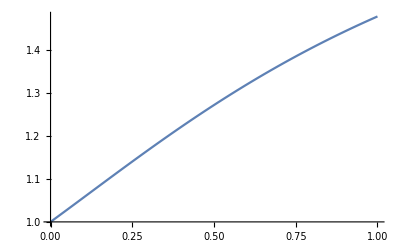

0

```mathematica
rsolct3[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]^2-(myNorm[ns]+myNormMass[ms-ns])^2)/(2*(ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]*(myNorm[ns]+myNormMass[ms-ns])))]

jacquesct3[ks_,ls_,ms_,ns_]:=(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->rsolct3[ks,ls,ms,ns]}


kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};

N[(myNorm[lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12]
N[(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct3[kt,lt,mt,nt]),12]

Plot[(myNorm[lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct3[kt,lt,mt+eps{1,1,0},nt]*(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct3[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]

N[myNorm[Exp[rsolct3[kt,lt,mt,nt]]*lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]+myNorm[Exp[rsolct3[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-myNormMass[mt-nt]-myNorm[nt],12]
```

```mathematica
fullCT32L[ks_,ls_,ms_,ns_]:=((1/(jacquesct3[ks,ls,ms,ns]*(Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-rsolct3[ks,ls,ms,ns]))*ct3integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->rsolct3[ks,ls,ms,ns]}
```

```mathematica
kt={1,1,0.5};
lt={0,0.5,1};
mt={0.5,3/2,1};
nt={0,1,0};

fullCT32L[kt,lt,mt,nt]
```

0.00463269

-(2 (-90-39 √6+10 √13+3 √78))/((√3 (-1+√2+√3) (1+√2+√3) (-5+4 √2-√13) (-3+2 √2+2 √3-√13) (1+√13) (5+√13) (5+4 √2+√13) (3+2 √2+2 √3+√13)) eps)+O[eps]^0

-(2 (-90-39 √6+10 √13+3 √78))/((√3 (-1+√2+√3) (1+√2+√3) (-5+4 √2-√13) (-3+2 √2+2 √3-√13) (1+√13) (5+√13) (5+4 √2+√13) (3+2 √2+2 √3+√13)) eps)+O[eps]^0

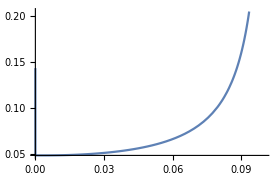

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};
Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT32L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]

Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT32L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 4

-Graphics-

Two loop

```mathematica
ct4LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3-m[0]))+1/((E1+E4+E5)*(E0+E1+E3-m[0])*(E2+E3-m[0]))+1/((E1+E4+E5)*(E2+E3-m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E1+E2+E4-q[0]))+1/((E1+E4+E5)*(E0+E4-q[0])*(E1+E2+E4-q[0]))+1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E2+E5-q[0]))+1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E3+E5-m[0]-q[0]))+1/((E2+E3-m[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E3-m[0]))-1/((E1+E4+E5) (E0+E1+E3-m[0]) (E2+E3-m[0]))-1/((E1+E4+E5) (E2+E3-m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E1+E2+E4-q[0]))-1/((E1+E4+E5) (E0+E4-q[0]) (E1+E2+E4-q[0]))-1/((E0+E1+E2) (E1+E2+E4-q[0]) (E2+E5-q[0]))-1/((E0+E4-q[0]) (E1+E2+E4-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E0+E1+E3-m[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E3-m[0]) (E2+E3-m[0]) (E3+E5-m[0]-q[0]))-1/((E2+E3-m[0]) (E0+E4-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0])))

```mathematica
ct4integrand1[ks_,ls_,ms_,ns_]:=ct4LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
a4[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls])^2-myNorm[ls]^2)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2
b4[ks_,ls_,ms_,ns_]:=-2(myNorm[ks]+myNorm[ks-ls])(myNormMass[ms-ns]+myNorm[ns])/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+2*(ls.ms)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]
c4[ks_,ls_,ms_,ns_]:=(myNormMass[ms-ns]+myNorm[ns])^2-myNorm[ms]^2

rsol=Solve[t*myNorm[{kx,ky,kz}]/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]+t*myNorm[{kx,ky,kz}-{lx,ly,lz}]/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]+myNorm[t*{lx,ly,lz}/Sqrt[myNorm[{kx,ky,kz}]^2+myNorm[{lx,ly,lz}]^2]-{mx,my,mz}]-myNormMass[{mx,my,mz}-{nx,ny,nz}]-myNorm[{nx,ny,nz}]==0,t];

rsolct4[ks_,ls_,ms_,ns_]:=Log[(-b4[ks,ls,ms,ns]-Sqrt[b4[ks,ls,ms,ns]^2-4c4[ks,ls,ms,ns] a4[ks,ls,ms,ns]])/(2a4[ks,ls,ms,ns])]
rsolct4Brute[ks_,ls_,ms_,ns_]:=Log[t/.rsol[[1]]]/.{kx->ks[[1]],ky->ks[[2]],kz->ks[[3]],lx->ls[[1]],ly->ls[[2]],lz->ls[[3]],mx->ms[[1]],my->ms[[2]],mz->ms[[3]],nx->ns[[1]],ny->ns[[2]],nz->ns[[3]]}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+√2+√3-(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2)).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2))+(-(-12+6 √6-(3 √2 (-3+Power[«2»]))/Plus[«3»]-6 √Times[«2»])/(√3)-√(1/3 Power[«2»]-16 Plus[«6»]))/(4 √6)+1/(√(3/(1/32 Plus[«2»]^2+1/64 Plus[«2»]^2)))+√(1+(-1+(Times[«3»]+Times[«2»])/(8 √3))^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[3]/2-Log[(3 (-2/(√3)+(2 (Power[«2»]+Power[«2»]) (Times[«3»]+Power[«2»]))/(√3)-√Plus[«2»]))/(2 (-1+Plus[«2»]^2))].

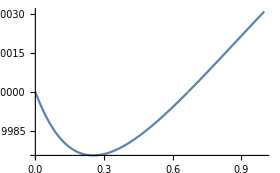

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2))+(-2+((-3+Power[«2»])/(2 Plus[«3»])+√(3+Times[«3»]))^2)/(2 √3 (-1/(√3)+(1/2 Power[«2»] Plus[«2»]+√Plus[«2»])/(√3)))+√(1+(-1+(2+Times[«2»])/(2 √3 Plus[«2»]))^2).

```mathematica
jacquesct4[ks_,ls_,ms_,ns_]:=(Exp[r]*(myNorm[ks]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+myNorm[ks-ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]*(myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->rsolct4[ks,ls,ms,ns]}


kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
N[rsolct4[kt,lt,mt,nt],12];
N[rsolct4Brute[kt,lt,mt,nt],12];

N[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12];
N[(myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]kt]/Sqrt[myNorm[kt]^2+myNorm[lt]^2]+myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]kt-Exp[rsolct4Brute[kt,lt,mt,nt]]lt]/Sqrt[myNorm[kt]^2+myNorm[lt]^2]+myNorm[Exp[rsolct4Brute[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]-myNormMass[mt-nt]-myNorm[nt]),12];
N[(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct4[kt,lt,mt,nt]),12];

Plot[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct4[kt,lt,mt+eps{1,1,0},nt]*(Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-rsolct4[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]

N[myNorm[Exp[rsolct3[kt,lt,mt,nt]]*lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]-mt]+myNorm[Exp[rsolct3[kt,lt,mt,nt]]lt/Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-myNormMass[mt-nt]-myNorm[nt],12];
```

```mathematica
fullCT42L[ks_,ls_,ms_,ns_]:=((1/(jacquesct4[ks,ls,ms,ns]*(Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-rsolct4[ks,ls,ms,ns]))*ct4integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->rsolct4[ks,ls,ms,ns]}
```

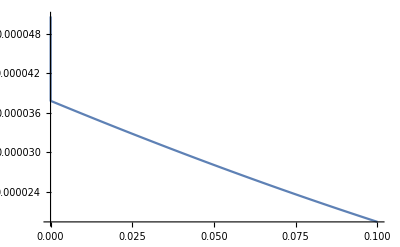

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
(*Series[integrand1[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]
Series[fullCT42L[kt,lt,mt+eps{1,1,0},nt],{eps,0,-1}]*)

Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT42L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

One loop

```mathematica
rsolct5[ks_,ls_,ms_,ns_]:=Log[(myNorm[ls]^2-(myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])^2)/(2*(myNorm[ks]*(myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])+ks.ls))*myNorm[ks]]
jacquesct5[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]ks/myNorm[ks]-ls]))/.{r->rsolct5[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1+√2+√3-(-3+(1+√2+√3)^2)/(2 (1+√2+√3))-√(3+(3+Times[«2»])^2/(4 (1+Power[«2»]+Power[«2»])^2)).

0.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[2]/2-Log[(1-Plus[«3»]^2)/(2 (1-1/2 Power[«2»] Plus[«2»]-Power[«2»]))].

0.

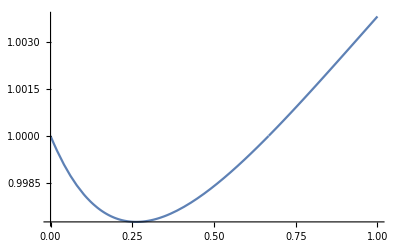

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
N[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt]),12]
N[(Log[myNorm[kt]]-rsolct5[kt,lt,mt,nt]),12]
Plot[(myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt-eps{1,1,0}]-myNormMass[mt+eps{1,1,0}-nt]-myNorm[nt])/(jacquesct5[kt,lt,mt+eps{1,1,0},nt]*(Log[myNorm[kt]]-rsolct5[kt,lt,mt+eps{1,1,0},nt])),{eps,0,1}]
```

```mathematica
fullCT41L[ks_,ls_,ms_,ns_]:=((1/(jacquesct5[ks,ls,ms,ns]*(Log[myNorm[ks]]-rsolct5[ks,ls,ms,ns]))*ct4integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->rsolct5[ks,ls,ms,ns]}
```

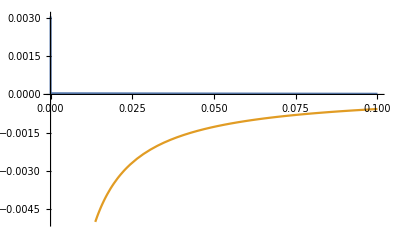

```mathematica
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT41L[kt,lt,mt+eps{1,0,1},nt],fullCT41L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 5

-Graphics-

```mathematica
ct5LTD=-(1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3+m[0]))+1/((E1+E4+E5)*(E0+E1+E3+m[0])*(E2+E3+m[0]))+1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E0+E4-q[0]))+1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E0+E4-q[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E2+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))+1/((E1+E4+E5)*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3+m[0]))+1/((E1+E4+E5)*(E2+E3+m[0])*(E0+E4-q[0]))+1/((E0+E1+E2)*(E2+E3+m[0])*(E2+E5-q[0]))+1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0]))+1/((E0+E1+E2)*(E1+E4+E5)*(E1+E3+E4-m[0]-q[0]))+1/((E1+E4+E5)*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))+1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])))/(64*E0*E1*E2*E3*E4*E5)
```

1/(64 E0 E1 E2 E3 E4 E5)(-1/((E0+E1+E2) (E1+E4+E5) (E0+E1+E3+m[0]))-1/((E0+E1+E2) (E1+E4+E5) (E2+E3+m[0]))-1/((E1+E4+E5) (E0+E1+E3+m[0]) (E2+E3+m[0]))-1/((E0+E1+E2) (E0+E1+E3+m[0]) (E0+E4-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E0+E4-q[0]))-1/((E0+E1+E3+m[0]) (E2+E3+m[0]) (E0+E4-q[0]))-1/((E0+E1+E2) (E2+E3+m[0]) (E2+E5-q[0]))-1/((E1+E4+E5) (E2+E3+m[0]) (E2+E5-q[0]))-2/((E2+E3+m[0]) (E0+E4-q[0]) (E2+E5-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5) (E0+E4-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2) (E1+E4+E5) (E3+E5-m[0]-q[0]))-1/((E0+E1+E2) (E0+E4-q[0]) (E3+E5-m[0]-q[0]))-1/((E1+E4+E5) (E2+E5-q[0]) (E3+E5-m[0]-q[0]))-1/((E0+E4-q[0]) (E2+E5-q[0]) (E3+E5-m[0]-q[0])))

Two loop

```mathematica
ct5integrand1[ks_,ls_,ms_,ns_]:=ct5LTD/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ms-ns]+myNorm[ns],m[0]->-myNorm[ms]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
radius5[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ms-ns]+myNorm[ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(myNorm[ks]+myNorm[ks-ls]+myNorm[ls])]
jacques5[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls]+myNorm[ls])Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/.{r->radius5[ks,ls,ms,ns]}
```

```mathematica
fullCT52L[ks_,ls_,ms_,ns_]:=((1/(jacques5[ks,ls,ms,ns] (Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*ct5integrand1[t*ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]})/.{r->radius5[ks,ls,ms,ns]}
```

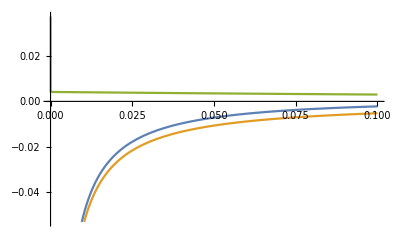

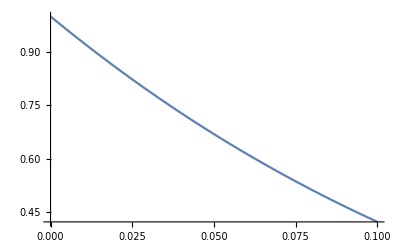

```mathematica
kt={1,0,0};
lt={-1/2,0,1};
mt={0,1,1};
nt={a,a,0}/.{a->1/977388(566957-156540 √2-282450 √5+14530 √10-3730 √13+112770 √26+32085 √65-38720 √130-√(1208768726560-438553801896 √2-95049382632 √5+65571421352 √10-52749692552 √13-14120108088 √26+89793904224 √65-70456909480 √130))};


Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt],fullCT52L[kt,lt,mt+eps{1,0,1},nt],integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT52L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt]/fullCT52L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

One loop

```mathematica
radius51L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])^2-myNorm[ls]^2)/(2(-(myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])-ks.ls/myNorm[ks]))]
jacques51L[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->radius51L[ks,ls,ms,ns]}
```

```mathematica
fullCT51L[ks_,ls_,ms_,ns_]:=((1/(jacques51L[ks,ls,ms,ns] (Log[myNorm[ks]]-r))*ct5integrand1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->radius51L[ks,ls,ms,ns]}
```

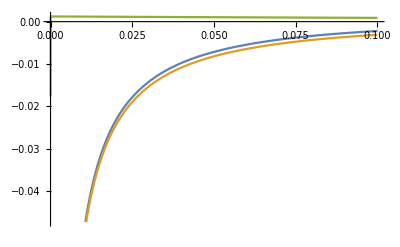

```mathematica
Plot[{integrand1[kt,lt,mt+eps{1,0,1},nt],fullCT51L[kt,lt,mt+eps{1,0,1},nt],integrand1[kt,lt,mt+eps{1,0,1},nt]-fullCT51L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

### Full integrand

```mathematica
integrand11L[ks_,ls_,ms_,ns_]:=(fullCT11L[ks,ls,ms,ns]+fullCT41L[ks,ls,ms,ns]+fullCT51L[ks,ls,ms,ns])
integrand12L[ks_,ls_,ms_,ns_]:=(fullCT12L[ks,ls,ms,ns]+fullCT22L[ks,ls,ms,ns]+fullCT32L[ks,ls,ms,ns]+fullCT42L[ks,ls,ms,ns]+fullCT52L[ks,ls,ms,ns])
```

#### MultiChanneling

```mathematica
eSurf1[ks_,ls_,ms_,ns_]:=(myNorm[ls]+myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns])
eSurf2[ks_,ls_,ms_,ns_]:=(2*myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns])
pSurf1[ks_,ls_,ms_,ns_]:=(myNorm[ls]+myNorm[ls-ms]-myNorm[ms])
```

```mathematica
subspaceTheta[ks_,ls_,ms_,ns_]:=HeavisideTheta[eSurf1[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]HeavisideTheta[eSurf2[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]
fullspaceTheta[ks_,ls_,ms_,ns_]:=1-HeavisideTheta[eSurf1[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]HeavisideTheta[eSurf2[ks,ls,ms,ns]^2-pSurf1[ks,ls,ms,ns]^2]
```

#### Full Integrand

```mathematica
fullintegrand1[ks_,ls_,ms_,ns_]:=-1/(8 myNorm[ns] myNormMass[ns-ms] myNorm[ms])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ms],ns[[1]],ns[[2]],ns[[3]]}])(integrand1[ks,ls,ms,ns]-subspaceTheta[ks,ls,ms,ns]integrand11L[ks,ls,ms,ns]-fullspaceTheta[ks,ls,ms,ns]integrand12L[ks,ls,ms,ns])
```

## -Graphics-

```mathematica
props2=prop[k,0]*prop[k-l,0]*prop[k+q,0]
diag2=cLTD[props2,loopmom->{k},EvalAll->True];
diag2[[1]]
diag2[[2]]
integrand2[ks_,ls_,ms_,ns_]:=-I*diag2[[1]]/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[k+q,0]

-(ⅈ (-1/((E0+E1+l[0]) (E0+E2-q[0]))-1/((E0+E1-l[0]) (E1+E2-l[0]-q[0]))-1/((E0+E2-q[0]) (E1+E2-l[0]-q[0]))-1/((E0+E1-l[0]) (E0+E2+q[0]))-1/((E0+E1+l[0]) (E1+E2+l[0]+q[0]))-1/((E0+E2+q[0]) (E1+E2+l[0]+q[0]))))/(8 E0 E1 E2)

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

### Counterterms

#### Threshold 1

-Graphics-

```mathematica
ct6LTD=-(-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0]))/(8 E0 E1 E2)
```

-(-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0]))/(8 E0 E1 E2)

```mathematica
ct1integrand2[ks_,ls_,ms_,ns_]:=ct6LTD/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
fullCT61L[ks_,ls_,ms_,ns_]:=((1/(2*Exp[r](Log[myNorm[ks]]-r))*ct1integrand2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->Log[(myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns])/2]}
```

0

0

0.138057

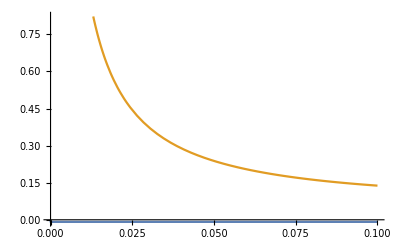

```mathematica
kt={(2+Sqrt[2]+Sqrt[3])/2,0,0};
lt={0,0,1};
mt={0,1,1};
nt={1,1,1};

2*myNorm[kt]-(myNorm[lt]+myNorm[mt-lt]+myNormMass[mt-nt]+myNorm[nt])

(Log[myNorm[kt]]-r)/.{r->Log[(myNorm[lt]+myNorm[mt-lt]+myNormMass[mt-nt]+myNorm[nt])/(2)]}

fullCT61L[kt,lt,mt+0.1{1,0,1},nt]

Plot[{integrand2[kt,lt,mt+eps{1,0,1},nt]-fullCT61L[kt,lt,mt+eps{1,0,1},nt],fullCT61L[kt,lt,mt+eps{1,0,1},nt]},{eps,0,0.1}]
```

#### Threshold 2

-Graphics-

```mathematica
ct7LTD=-(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)
```

-(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)

```mathematica
ct2integrand2[ks_,ls_,ms_,ns_]:=ct7LTD/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ms-ls]+myNormMass[ms-ns]+myNorm[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
rsol7[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ms]+myNormMass[ms-ns]+myNorm[ns])^2-myNorm[ls]^2)/(2(myNorm[ls-ms]+myNormMass[ms-ns]+myNorm[ns]-ks.ls/myNorm[ks]))]
jacques7[ks_,ls_,ms_,ns_]:=(Exp[r]*(1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->rsol7[ks,ls,ms,ns]}
```

```mathematica
fullCT71L[ks_,ls_,ms_,ns_]:=((1/(jacques7[ks,ls,ms,ns]*(Log[myNorm[ks]]-r))*ct2integrand2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]})/.{r->rsol7[ks,ls,ms,ns]}
```

-(-1/(1+√2+√3)-1/(-2+2 √3-1/4 √(27-17 √2+√3-√6)-√(3+1/16 (27-17 √2+√3-√6))))/(24 √2)

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+√2+√3-1/4 √(27-17 √2+√3-√6)-√(3+1/16 (27-17 Power[«2»]+√3-Power[«2»])).

0.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[3]/2-Log[(-1+(1+Times[«2»]+Power[«2»])^2)/(2 (1-Power[«2»]+1/4 Power[«2»]+√Plus[«2»]))].

0.

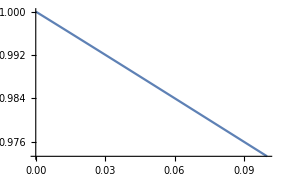

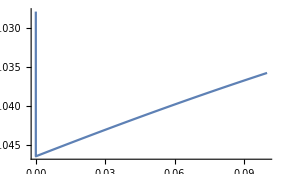

```mathematica
kt={1,1,1};
lt={0,1,0};
mt={0,1,1};
nt={1/4 √(27-17 √2+√3-√6),0,0};

ct2integrand2[kt,lt,mt,nt]
N[myNorm[kt]+myNorm[kt-lt]-myNorm[lt-mt]-myNormMass[mt-nt]-myNorm[nt],12]
N[Log[myNorm[kt]]-rsol7[kt,lt,mt,nt],12]
Plot[(myNorm[kt]+myNorm[kt-lt]-myNorm[lt-mt-eps{1,0,1}]-myNormMass[mt+eps{1,0,1}-nt]-myNorm[nt])/(jacques7[kt,lt,mt+eps{1,0,1},nt](Log[myNorm[kt]]-rsol7[kt,lt,mt+eps{1,0,1},nt])),{eps,0,0.1}]

Plot[{integrand2[kt,lt,mt+eps{1,1,1/2},nt]-fullCT71L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### Full Integrand

```mathematica
integrand21L[ks_,ls_,ms_,ns_]:=(fullCT61L[ks,ls,ms,ns]+fullCT71L[ks,ls,ms,ns])
```

```mathematica
fullintegrand2[ks_,ls_,ms_,ns_]:=1/(16 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])(integrand2[ks,ls,ms,ns]-integrand21L[ks,ls,ms,ns])
```

## -Graphics-

### Full Integrand

```mathematica
fullintegrand3[ks_,ls_,ms_,ns_]:=1/(32 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls-ks]myNorm[ks])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls]+myNorm[ls-ks],ks[[1]],ks[[2]],ks[[3]]}])1/(MS[{myNorm[ks-ls]+myNorm[ks],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ks-ls]+myNorm[ks],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ks-ls]+myNorm[ks]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])
```

## Full integrand

```mathematica
fullintegrand[ks_,ls_,ms_,ns_]:=fullintegrand1[ks,ls,ms,ns]+fullintegrand2[ks,ls,ms,ns]+fullintegrand3[ks,ls,ms,ns]
```

## TESTS

### Single threshold

-Graphics-

```mathematica
kt={1+Sqrt[3]/2,0,0};
lt={0,1,0};
mt={0,0,1};
nt={0,1,0};
```

```mathematica
fullintegrand2[kt,lt,mt+0.1{1,0,1},nt]
```

-7.84572×10^-10

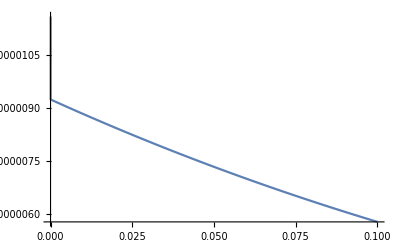

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={0,1,0};
lt={1+Sqrt[3]/2,0,0};
mt={0,0,1};
nt={0,1,0};
```

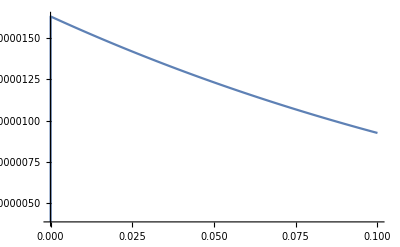

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,3/2,1};
nt={0,1,0};
```

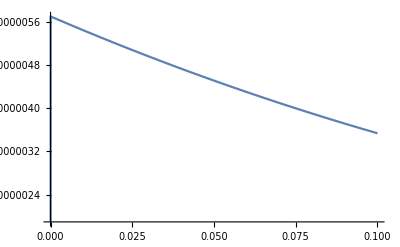

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt](*-fullCT32L[kt,lt,mt+eps{1,0,1},nt],fullCT11L[kt,lt,mt+eps{1,0,1},nt],fullCT12L[kt,lt,mt+eps{1,0,1},nt]*)},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,1,0};
lt={0,0,1};
mt={0,1,1};
nt={(3-(Sqrt[2]+Sqrt[3]+1)^2)/(2(Sqrt[2]+Sqrt[3]+1)),0,0};
```

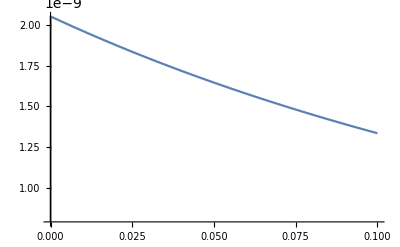

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={1,0,0};
lt={-1/2,0,1};
mt={0,1,1};
nt={a,a,0}/.{a->1/977388(566957-156540 √2-282450 √5+14530 √10-3730 √13+112770 √26+32085 √65-38720 √130-√(1208768726560-438553801896 √2-95049382632 √5+65571421352 √10-52749692552 √13-14120108088 √26+89793904224 √65-70456909480 √130))};
```

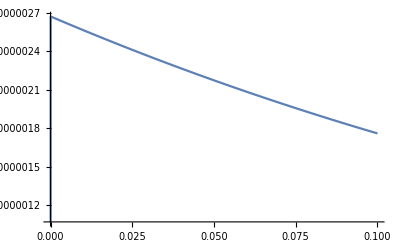

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

```mathematica
kt={(2+Sqrt[2]+Sqrt[3])/2,0,0};
lt={0,0,1};
mt={0,1,1};
nt={1,1,1};
```

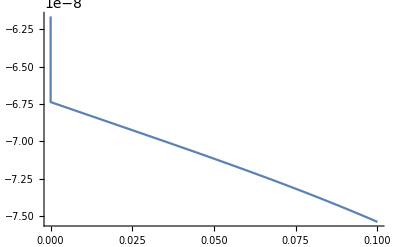

```mathematica
Plot[{fullintegrand[kt,lt,mt+eps{1,0,1},nt]},{eps,0.0,0.1}]
```

-Graphics-

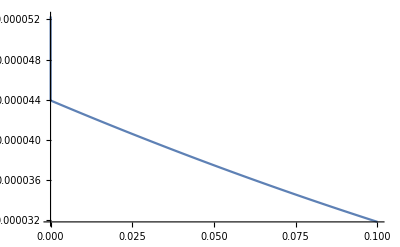

```mathematica
kt={1,1,1};
lt={0,1,0};
mt={0,1,1};
nt={1/4 √(27-17 √2+√3-√6),0,0};


Plot[{fullintegrand[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### Pinches

-Graphics-

```mathematica
kt={0.5,0,0};
lt={1,0,0};
mt={0,0,1};
nt={0,1,0};
```

```mathematica
pSurf1[kt,lt,mt,nt]
```

√2

```mathematica
subspaceTheta[kt,lt,mt,nt]
```

0

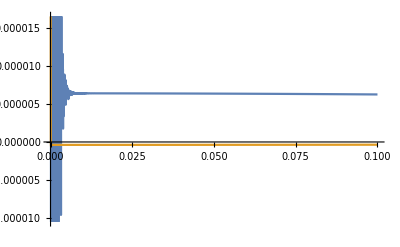

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt],fullintegrand2[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
kt={0,0,1};
lt={0.5,0,0};
mt={1,0,0};
nt={0,1,0};
```

```mathematica
subspaceTheta[kt,lt,mt,nt]
```

1

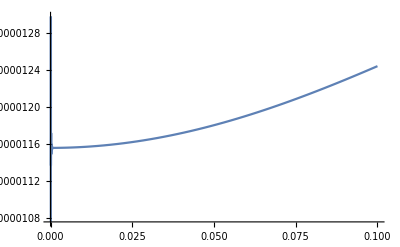

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt]+fullintegrand2[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
kt={0.3,0,0};
lt={0.5,0,0};
mt={1,0,0};
nt={0,1,0};
```

```mathematica
pSurf1[kt,lt,mt,nt]
```

0.

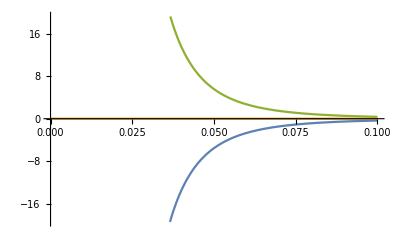

```mathematica
Plot[{fullCT11L[kt,lt+eps{0,1,1},mt,nt],fullCT41L[kt,lt+eps{0,1,1},mt,nt],fullCT51L[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

```mathematica
(*fullintegrand1[ks_,ls_,ms_,ns_]:=-1/(8 myNorm[ns] myNormMass[ns-ms] myNorm[ms])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ms],ns[[1]],ns[[2]],ns[[3]]}])(0*integrand1[ks,ls,ms,ns]-subspaceTheta[ks,ls,ms,ns]integrand11L[ks,ls,ms,ns]-fullspaceTheta[ks,ls,ms,ns]integrand12L[ks,ls,ms,ns])
fullintegrand2[ks_,ls_,ms_,ns_]:=1/(16 myNorm[ns] myNormMass[ns-ms] myNorm[ms-ls]myNorm[ls])1/(MS[{myNormMass[ms-ns]+myNorm[ns],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNormMass[ms-ns]+myNorm[ns]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls],ms[[1]],ms[[2]],ms[[3]]}])1/(MS[{myNorm[ms-ls]+myNorm[ls]+myNormMass[ms-ns],ns[[1]],ns[[2]],ns[[3]]}])(0*integrand2[ks,ls,ms,ns]-integrand21L[ks,ls,ms,ns])*)
```

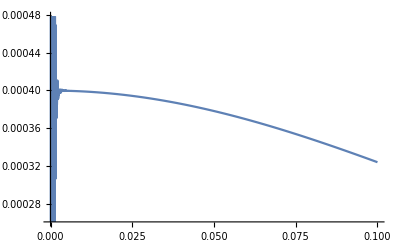

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,0},mt,nt]+fullintegrand3[kt,lt+eps{0,1,0},mt,nt]+fullintegrand2[kt,lt+eps{0,1,0},mt,nt],},{eps,0,0.1}]
```

### Intersection of thresholds and pinches

-Graphics-

The intersection does not exist (it would imply the decay of a massless particle into two massless particles and a massive particle)

-Graphics-

The intersection does not exist (it would imply the decay of a massless particle into a massless particle and a massive particle)

-Graphics-

```mathematica
eSurfTest1[ks_,ls_,ms_,ns_]:=2*myNorm[ks]-myNorm[ls]-myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns]
eSurfTest2[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ms]-myNorm[ms]
```

```mathematica
Solve[eSurfTest1[{0,a,0},{1/2,0,0},{1,0,0},{0,0,1}]==0,a]
```

{{a→1/2 (-2-√3)},{a→1/2 (2+√3)}}

```mathematica
kt={0,1/2 (2+√3),0};
lt={1/2,0,0};
mt={1,0,0};
nt={0,0,1};
N[eSurfTest1[kt,lt,mt,nt],12]
N[eSurfTest2[kt,lt,mt,nt],12]
```

0

0

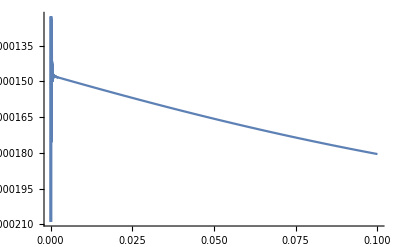

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand3[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand2[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
eSurfTest3[ks_,ls_,ms_,ns_]:=myNorm[ks]+myNorm[ks-ls]-myNorm[ls-ms]-myNormMass[ms-ns]-myNorm[ns]
eSurfTest4[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ms]-myNorm[ms]
```

```mathematica
Solve[eSurfTest3[{0,a,0},{1/2,0,0},{1,0,0},{0,0,1}]==0,a]
```

{{a→-√(2/3 (2+√3))},{a→√(2/3 (2+√3))}}

```mathematica
kt={0,√(2/3 (2+√3)),0};
lt={1/2,0,0};
mt={1,0,0};
nt={0,0,1};
N[eSurfTest3[kt,lt,mt,nt],12]
N[eSurfTest4[kt,lt,mt,nt],12]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3/2-√3+√(2/3 (2+√3))+√(1/4+2/3 (2+√3)).

0.

0

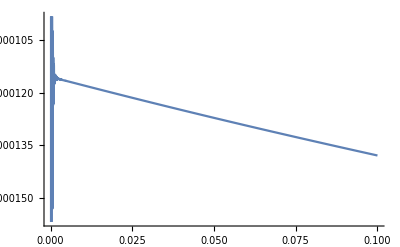

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand3[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand2[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
eSurfTest5[ks_,ls_,ms_,ns_]:=myNorm[ks]+myNorm[ks-ls]+myNorm[ls]-myNorm[ms]-myNormMass[ms-ns]-myNorm[ns]
eSurfTest6[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ms]-myNorm[ms]
```

```mathematica
Solve[eSurfTest5[{0,a,0},{1/2,0,0},{1,0,0},{0,0,1}]==0,a]
```

{{a→-√(2/3 (2+√3))},{a→√(2/3 (2+√3))}}

```mathematica
kt={0,√(2/3 (2+√3)),0};
lt={1/2,0,0};
mt={1,0,0};
nt={0,0,1};
N[eSurfTest5[kt,lt,mt,nt],12]
N[eSurfTest6[kt,lt,mt,nt],12]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3/2-√3+√(2/3 (2+√3))+√(1/4+2/3 (2+√3)).

0.

0

```mathematica
Plot[{fullintegrand1[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand3[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]+fullintegrand2[kt,lt+eps{0,1,1},mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

-Graphics-

## -Graphics-

## -Graphics-

#### Integrand

```mathematica
props1=prop[k,0]*prop[k-l,0]*prop[l,0]*prop[k+q,0]*prop[l-m,0]*prop[l+q,0]*prop[l-n+q,0]
diag1=cLTD[props1,loopmom->{k,l},EvalAll->True];
CForm[diag1[[1]]]
diag1[[2]]
integrand1[ks_,ls_,ms_,ns_]:=diag1[[1]]/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[l,0] prop[l-m,0] prop[k+q,0] prop[l+q,0] prop[l-n+q,0]

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

-0.0078125*(-(1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E1 + E2 + E4 - q(0)))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E1 + E2 + E4 - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E2 + E5 - q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) - 
      1/((E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E5 + E6 + n(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E4 + E6 - n(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E5 + E6 + n(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E5 + E6 - n(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 - n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E5 + E6 - n(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E1 + E2 + E4 - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E2 + E3 + m(0))*(E0 + E4 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E5 + E6 + n(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E2 + E3 - m(0))*(E0 + E4 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E2 + E5 - q(0))*(E1 + E3 + E4 - m(0) - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E0 + E1 + E5 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E1 + E2 + E4 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E5 + E6 + n(0))*(E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E1 + E2 + E4 - q(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E5 + E6 + n(0))*(E0 + E4 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E4 - q(0))*(E2 + E5 - q(0))*(E0 + E1 + E6 + n(0) - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) - 1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 - n(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E2 + E6 + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E2 + E6 + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E5 + E6 + n(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E3 + E5 - m(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E2 + E5 - q(0))*(E2 + E6 + n(0) - q(0))*(E3 + E6 - m(0) + n(0) - q(0))*(E0 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E1 + E2 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E1 + E2 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E2 + E5 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) - 1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E2 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) - 
      1/((E2 + E3 - m(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E5 + E6 - n(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E5 + E6 - n(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E4 + E6 + n(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E5)*(E5 + E6 + n(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 + n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E5 + E6 + n(0))*(E0 + E4 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E5)*(E5 + E6 + n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E5 + E6 + n(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 + n(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E1 + E4 + E6 + n(0))*(E0 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E3 - m(0))*(E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E5 + E6 - n(0))*(E1 + E2 + E4 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 - m(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E1 + E4 + E6 - n(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E2 + E3 - m(0))*(E0 + E4 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E5 + E6 - n(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E5 + E6 - n(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E3 + m(0))*(E0 + E4 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E1 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E3 + m(0))*(E2 + E3 + m(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E2 + E3 + m(0))*(E0 + E4 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E2 + E5 + q(0))*(E1 + E3 + E4 + m(0) + q(0))*(E3 + E5 + m(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E0 + E4 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E0 + E1 + E5 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E5 + E6 - n(0))*(E1 + E2 + E4 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E5 + E6 - n(0))*(E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E0 + E4 - q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E1 + E2)*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E1 + E2 + E4 + q(0))*(E2 + E5 + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E5 + E6 - n(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E5 + E6 - n(0))*(E0 + E4 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E1 + E4 + E6 - n(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))) - 
      1/((E0 + E4 + q(0))*(E2 + E5 + q(0))*(E0 + E1 + E6 - n(0) + q(0))*(E2 + E6 - n(0) + q(0))*(E3 + E6 + m(0) - n(0) + q(0))))/(E0*E1*E2*E3*E4*E5*E6)

```mathematica
pinch1[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ms]-myNorm[ms]
pinch2[ks_,ls_,ms_,ns_]:=myNorm[ls-ns]+myNorm[ls-ms]-myNorm[ms-ns]
esurf1[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ns]-myNorm[ms]-myNorm[ms-ns]
esurf2[ks_,ls_,ms_,ns_]:=2*myNorm[ls]-myNorm[ms]-myNorm[ms-ns]-myNormMass[ns]
esurf3[ks_,ls_,ms_,ns_]:=myNorm[ls]+myNorm[ls-ms]-myNorm[ms-ns]-myNormMass[ns]

subspaceThetaxSec1[ks_,ls_,ms_,ns_]:=If[Or[And[(*esurf1[ks,ls,ms,ns]^2>pinch1[ks,ls,ms,ns]^2,*)esurf2[ks,ls,ms,ns]^2>pinch1[ks,ls,ms,ns]^2(*,esurf3[ks,ls,ms,ns]^2>pinch1[ks,ls,ms,ns]^2*)],And[(*esurf1[ks,ls,ms,ns]^2>pinch2[ks,ls,ms,ns]^2,*) esurf2[ks,ls,ms,ns]^2>pinch2[ks,ls,ms,ns]^2(*,esurf3[ks,ls,ms,ns]^2>pinch2[ks,ls,ms,ns]^2]*)]],1,0]

notsubspaceThetaxSec1[ks_,ls_,ms_,ns_]:=1-subspaceThetaxSec1[ks,ls,ms,ns]
```

### -Graphics-

```mathematica
cLTD11=-(-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E1+E2+E4-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6+n[0])*(E1+E2+E4-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6-n[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6-n[0])*(E0+E1+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E5+E6-n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E5+E6+n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5)*(E1+E4+E6-n[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5)*(E5+E6+n[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E5+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E5+E6-n[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E5+E6-n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E3-m[0])*(E5+E6+n[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E2+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E3-m[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E5-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E2+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E2+E5+q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E5+E6+n[0])*(E2+E5+q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E5+E6+n[0])*(E2+E5+q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E3+E5+m[0]+q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6+n[0])*(E3+E5+m[0]+q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6+n[0])*(E3+E5+m[0]+q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6+n[0])*(E3+E5+m[0]+q[0]))-1/((E1+E4+E5)*(E1+E4+E6-n[0])*(E2+E5+q[0])*(E3+E5+m[0]+q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E2+E5+q[0])*(E3+E5+m[0]+q[0]))-1/((E1+E4+E5)*(E5+E6+n[0])*(E2+E5+q[0])*(E3+E5+m[0]+q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E5+E6-n[0])*(E2+E6-n[0]+q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E2+E6-n[0]+q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E2+E5+q[0])*(E2+E6-n[0]+q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E2+E5+q[0])*(E2+E6-n[0]+q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6-n[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6-n[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E3+E5+m[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E3+E5+m[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E3+E5+m[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E2)*(E2+E5+q[0])*(E3+E5+m[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E1+E4+E6-n[0])*(E2+E5+q[0])*(E3+E5+m[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E2+E6-n[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E1+E4+E6-n[0])*(E5+E6-n[0])*(E2+E6-n[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E0+E1+E2)*(E2+E5+q[0])*(E2+E6-n[0]+q[0])*(E3+E6+m[0]-n[0]+q[0]))-1/((E1+E4+E6-n[0])*(E2+E5+q[0])*(E2+E6-n[0]+q[0])*(E3+E6+m[0]-n[0]+q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
integrand1CT1[ks_,ls_,ms_,ns_]:=cLTD11/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r1CT12L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ns]+myNorm[ms-ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2myNorm[ks])]
jacques1CT12L[ks_,ls_,ms_,ns_]:=(2*Exp[r]myNorm[ks]/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/.{r->r1CT12L[ks,ls,ms,ns]}
```

```mathematica
full1CT12L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT12L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT1[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT12L[ks,ls,ms,ns]}
```

-0.0000384196765102

0

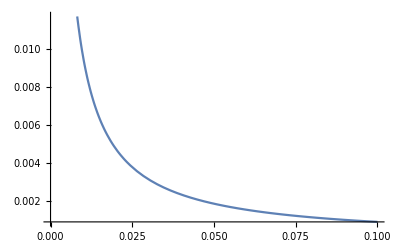

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/14 √(15/2 (79-52 √2)),0,0};

(*Solve[2*myNorm[kt]-(myNorm[mt]+myNormMass[nt]+myNorm[mt-nt])==0,a]*)
N[integrand1[kt,lt,mt+{1,1,1/2},nt],12]
N[full1CT12L[kt,lt,mt+{1,1,1/2},nt],12]
Plot[{integrand1[kt,lt,mt+eps{1,1,1/2},nt]-full1CT12L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

```mathematica
r1CT11L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ns]+myNorm[ms-ns])/2]
jacques1CT11L[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r1CT11L[ks,ls,ms,ns]}
```

```mathematica
full1CT11L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT11L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand1CT1[t*ks,ls,ms,ns]*subspaceThetaxSec1[t* ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r1CT11L[ks,ls,ms,ns]}
```

-0.0000384196765102

3.16691579351×10^-6

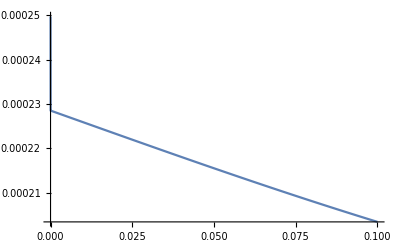

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/14 √(15/2 (79-52 √2)),0,0};

(*Solve[2*myNorm[kt]-(myNorm[mt]+myNormMass[nt]+myNorm[mt-nt])==0,a]*)
N[integrand1[kt,lt,mt+{1,1,1/2},nt],12]
N[full1CT11L[kt,lt,mt+{1,1,1/2},nt],12]
Plot[{integrand1[kt,lt,mt+eps{1,1,1/2},nt]-full1CT11L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### -Graphics--Graphics-

```mathematica
cLTD12=-(-1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3+m[0])*(E5+E6-n[0]))-1/((E1+E4+E5)*(E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6-n[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3+m[0])*(E1+E4+E6+n[0]))-1/((E1+E4+E5)*(E0+E1+E3+m[0])*(E2+E3+m[0])*(E1+E4+E6+n[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6-n[0])*(E0+E4-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6-n[0])*(E0+E4-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6-n[0])*(E2+E5-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E5+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E5+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E1+E4+E6+n[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E5)*(E5+E6-n[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E5)*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E5+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6+n[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E4-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-(1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6-n[0])))-1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3+m[0])*(E5+E6+n[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E5+E6+n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5)*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E5)*(E5+E6+n[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E5+E6+n[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0])*(E2+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT2[ks_,ls_,ms_,ns_]:=cLTD12/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r1CT22L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ns]+myNorm[ms-ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(myNorm[ks]+myNorm[ks-ls]+myNorm[ls])]
jacques1CT22L[ks_,ls_,ms_,ns_]:=(Exp[r](myNorm[ks]+myNorm[ks-ls]+myNorm[ls])/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/.{r->r1CT22L[ks,ls,ms,ns]}
```

```mathematica
full1CT22L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT22L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT2[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT22L[ks,ls,ms,ns]}
```

0.804718956217

0.804718956217

1.75679379465×10^-7

0

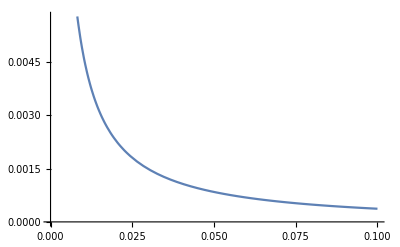

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/6 √(1/2 (192-101 √2+103 √5-39 √10)),0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]+myNorm[lt]-(myNorm[mt]+myNormMass[nt]+myNorm[mt-nt])==0,a]*)

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT22L[kt,lt,mt,nt],12]
N[integrand1[kt+{1,4,1/2},lt,mt+{1,0,1/2},nt+{1,0,1/2}],12]
N[full1CT22L[kt+{1,4,1/2},lt,mt+{1,0,1/2},nt+{1,0,1/2}],12]
Plot[{integrand1[kt,lt,mt+eps{1,1,1/2},nt]-full1CT22L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

```mathematica
r1CT21L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ms]+myNormMass[ns]+myNorm[ms-ns]-myNorm[ls])^2-myNorm[ls]^2)/(2(myNorm[ms]+myNormMass[ns]+myNorm[ms-ns]-myNorm[ls]-ks.ls/myNorm[ks]))]
jacques1CT21L[ks_,ls_,ms_,ns_]:=(Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]ks/myNorm[ks]-ls]))/.{r->r1CT21L[ks,ls,ms,ns]}
```

```mathematica
full1CT21L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT21L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand1CT2[t*ks,ls,ms,ns]*subspaceThetaxSec1[t* ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r1CT21L[ks,ls,ms,ns]}
```

0.69314718056

0.69314718056

1.75679379465×10^-7

-1.1020772679×10^-6

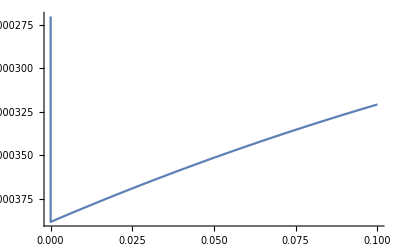

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/6 √(1/2 (192-101 √2+103 √5-39 √10)),0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]+myNorm[lt]-(myNorm[mt]+myNormMass[nt]+myNorm[mt-nt])==0,a]*)

N[Log[myNorm[kt]],12]
N[r1CT21L[kt,lt,mt,nt],12]
N[integrand1[kt+{1,4,1/2},lt,mt+{1,0,1/2},nt+{1,0,1/2}],12]
N[full1CT21L[kt+{1,4,1/2},lt,mt+{1,0,1/2},nt+{1,0,1/2}],12]
Plot[{integrand1[kt,lt,mt+eps{1,1,1/2},nt]-full1CT21L[kt,lt,mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

### -Graphics-

```mathematica
cLTD13=-(-1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E0+E4-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E4+E6-n[0])*(E1+E2+E4-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6-n[0])*(E0+E1+E5-q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E5-q[0]))-1/((E2+E3+m[0])*(E5+E6-n[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E5+E6-n[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E5)*(E5+E6-n[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E5)*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E5+E6-n[0])*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E0+E1+E6+n[0]-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E5+E6-n[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E5+E6-n[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E3+E5-m[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E5+E6-n[0])*(E3+E5-m[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E1+E4+E6+n[0])*(E3+E5-m[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E2+E6+n[0]-q[0])*(E0+E4+q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E6+n[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E6+n[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E6+n[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT3[ks_,ls_,ms_,ns_]:=cLTD13/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r1CT32L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNormMass[ns]+myNorm[ms-ns])Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2*myNorm[ls])]
jacques1CT32L[ks_,ls_,ms_,ns_]:=(2*Exp[r](myNorm[ls])/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/.{r->r1CT32L[ks,ls,ms,ns]}
```

```mathematica
full1CT32L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT32L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT3[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT32L[ks,ls,ms,ns]}
```

1.09861228867

1.09861228867

0.0000650743081115

0.0000490880476289

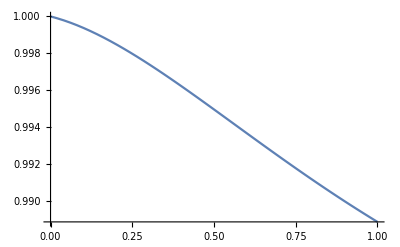

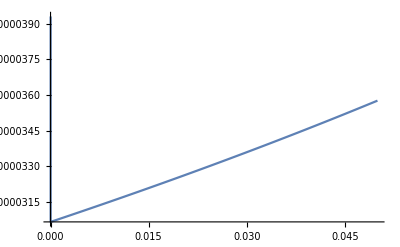

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/18 √(19/2 (137-34 √10)),0,0};

(*Solve[2*myNorm[lt]-(myNorm[mt]+myNormMass[nt]+myNorm[mt-nt])==0,a]*)

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT32L[kt,lt,mt,nt],12]
N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT32L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(2*myNorm[lt+eps{1,0,1/2}]-(myNorm[mt]+myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT32L[kt,lt+eps{1,0,1/2},mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt+eps{1,0,1/2}]^2]]-r1CT32L[kt,lt+eps{1,0,1/2},mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT32L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

### -Graphics-

```mathematica
cLTD14=-(-1/((E0+E1+E2)*(E2+E3+m[0])*(E5+E6+n[0])*(E1+E2+E4-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E1+E2+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E5+E6+n[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E0+E1+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E5+E6+n[0])*(E0+E4+q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E5+E6+n[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E2+E3+m[0])*(E2+E5-q[0])*(E0+E4+q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E6+n[0])*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT4[ks_,ls_,ms_,ns_]:=cLTD14/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}

r1CT42L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ms]+myNorm[ms-ns])^2-myNorm[ns]^2)Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2(myNorm[ls](myNorm[ms]+myNorm[ms-ns])-ls.ns))]

jacques1CT42L[ks_,ls_,ms_,ns_]:=(Exp[r](myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]myNorm[ls]^2/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2-ls.ns/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ns]))/.{r->r1CT42L[ks,ls,ms,ns]}
```

```mathematica
full1CT42L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT42L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT4[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT42L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√2+√5-√(2+(-4-Power[«2»])^2)+√(4+(-3-√10)^2).

0.

1.09861228867

1.09861228867

-5.68856310833×10^-9

0

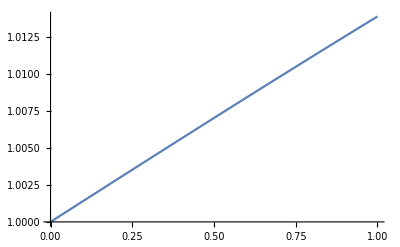

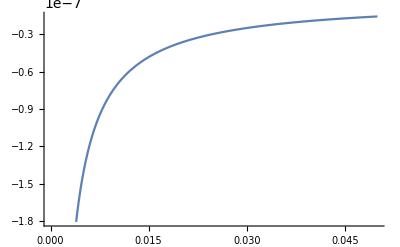

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={4+√10,0,0};

(*Solve[myNorm[lt]+myNorm[lt-nt]-(myNorm[mt]+myNorm[mt-nt])==0,a]*)
N[myNorm[lt]+myNorm[lt-nt]-(myNorm[mt]+myNorm[mt-nt]),12]

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT42L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT42L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(myNorm[lt]+myNorm[lt-nt-eps{1,0,1/2}]-(myNorm[mt]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT42L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT42L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT42L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

### -Graphics-

```mathematica
cLTD15=-(-1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3-m[0])*(E5+E6-n[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E2+E3-m[0])*(E1+E4+E6+n[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E5+E6-n[0])*(E0+E4-q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E0+E4-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E5+E6-n[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E1+E4+E6+n[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E5+E6-n[0])*(E2+E5-q[0]))-1/((E1+E4+E6-n[0])*(E5+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0]))-1/((E1+E4+E5)*(E5+E6-n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E1+E4+E5)*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E5+E6-n[0])*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E1+E3+E4-m[0]-q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E1+E4+E6+n[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E3-m[0])*(E0+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E3-m[0])*(E0+E4-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E1+E3+E4-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E5+E6-n[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E5+E6-n[0])*(E0+E4+q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E5+E6-n[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E1+E4+E6+n[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E5+E6-n[0])*(E2+E5-q[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E5+E6-n[0])*(E2+E5-q[0])*(E0+E4+q[0]))-1/((E1+E4+E5)*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E2+E3-m[0])*(E1+E4+E6+n[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0])*(E0+E4+q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT5[ks_,ls_,ms_,ns_]:=cLTD15/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}

r1CT52L[ks_,ls_,ms_,ns_]:=Log[((myNormMass[ns]+myNorm[ms-ns])^2-myNorm[ms]^2)Sqrt[myNorm[ks]^2+myNorm[ls]^2]/(2(myNorm[ls](myNormMass[ns]+myNorm[ms-ns])-ls.ms))]

jacques1CT52L[ks_,ls_,ms_,ns_]:=(Exp[r](myNorm[ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]myNorm[ls]^2/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->r1CT52L[ks,ls,ms,ns]}
```

```mathematica
full1CT52L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT52L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT5[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT52L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √5+√11-√(1+1/72 (188+35 Power[«2»]))-√(2+1/72 (188+35 Power[«2»])).

0.

1.09861228867

1.09861228867

-7.81616144794×10^-7

9.99365554819×10^-8

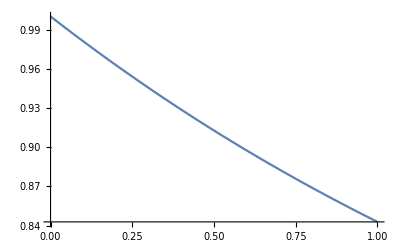

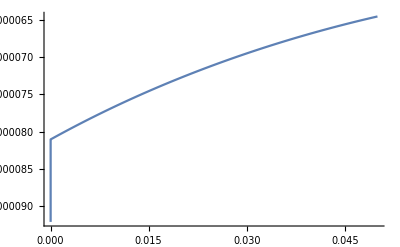

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/6 √(1/2 (188+35 √55)),0,0};

(*Solve[myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt]+myNorm[mt-nt])==0,a]*)
N[myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt]+myNorm[mt-nt]),12]

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT52L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT52L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT52L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT52L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT52L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

### -Graphics-

```mathematica
cLTD16=-(-1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3-m[0])*(E1+E4+E6-n[0]))-1/((E1+E4+E5)*(E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E4+E6-n[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E0+E1+E3-m[0])*(E5+E6+n[0]))-1/((E1+E4+E5)*(E0+E1+E3-m[0])*(E2+E3-m[0])*(E5+E6+n[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0]))-1/((E1+E4+E5)*(E2+E3-m[0])*(E5+E6+n[0])*(E0+E4-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E1+E4+E6-n[0])*(E1+E2+E4-q[0]))-1/((E0+E1+E2)*(E1+E4+E5)*(E5+E6+n[0])*(E1+E2+E4-q[0]))-1/((E1+E4+E5)*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))-1/((E1+E4+E5)*(E5+E6+n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E1+E4+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E1+E4+E6-n[0])*(E3+E5-m[0]-q[0]))-1/((E2+E3-m[0])*(E1+E4+E6-n[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6-n[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E1+E4+E6-n[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E3-m[0])*(E5+E6+n[0])*(E0+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E1+E2+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E1+E2+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E1+E2+E4-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E1+E3-m[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E3-m[0])*(E2+E3-m[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E2+E3-m[0])*(E0+E4-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E2+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E3+E5-m[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT6[ks_,ls_,ms_,ns_]:=cLTD16/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}


a62L[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls])^2-myNorm[ls]^2)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2
b62L[ks_,ls_,ms_,ns_]:=-2(myNormMass[ns]+myNorm[ms-ns])(myNorm[ks]+myNorm[ks-ls])/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+2ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2]
c62L[ks_,ls_,ms_,ns_]:=(myNormMass[ns]+myNorm[ms-ns])^2-myNorm[ms]^2

r1CT62L[ks_,ls_,ms_,ns_]:=Log[(-b62L[ks,ls,ms,ns]-Sqrt[b62L[ks,ls,ms,ns]^2-4 a62L[ks,ls,ms,ns]c62L[ks,ls,ms,ns]])/(2a62L[ks,ls,ms,ns])]

jacques1CT62L[ks_,ls_,ms_,ns_]:=(Exp[r](myNorm[ks]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+myNorm[ks-ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]myNorm[ls]^2/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2-ls.ms/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ms]))/.{r->r1CT62L[ks,ls,ms,ns]}
```

```mathematica
full1CT62L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT62L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT6[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT62L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2+√5+√11-√(1+(10358+2970 Power[«2»]+2826 Power[«2»]+1415 Power[«2»])/2888)-√(2+(10358+2970 Power[«2»]+2826 Power[«2»]+1415 Power[«2»])/2888).

0.

1.09861228867

1.09861228867

2.62650151941×10^-6

0

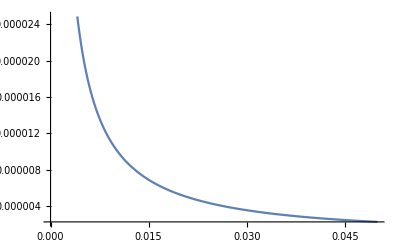

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/38 √(1/2 (10358+2970 √5+2826 √11+1415 √55)),0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-(myNormMass[nt]+myNorm[mt-nt])==0,a]*)
N[myNorm[kt]+myNorm[kt-lt]+myNorm[lt-mt]-(myNormMass[nt]+myNorm[mt-nt]),12]

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT62L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT62L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT52L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT52L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT62L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

```mathematica
r1CT61L[ks_,ls_,ms_,ns_]:=Log[((-myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns])^2-myNorm[ls]^2)/(2((-myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns])-ks.ls/myNorm[ks]))]

jacques1CT61L[ks_,ls_,ms_,ns_]:=(Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->r1CT61L[ks,ls,ms,ns]}
```

```mathematica
full1CT61L[ks_,ls_,ms_,ns_]:=HeavisideTheta[(myNorm[ms-ns]+myNormMass[ns]-myNorm[ms-ls])^2-myNorm[ls]^2](1/(jacques1CT61L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand1CT6[t*ks,ls,ms,ns]*subspaceThetaxSec1[t* ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r1CT61L[ks,ls,ms,ns]}
```

0.69314718056

0.69314718056

2.62650151941×10^-6

8.69275726104×10^-9

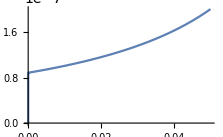

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/38 √(1/2 (10358+2970 √5+2826 √11+1415 √55)),0,0};


N[Log[myNorm[kt]],12]
N[r1CT61L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT61L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT52L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT52L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT61L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

### -Graphics-

```mathematica
cLTD17=-(-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E1+E4+E6+n[0])*(E5+E6+n[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E5+E6+n[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E2)*(E0+E1+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))-1/((E0+E1+E3+m[0])*(E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E5+E6+n[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E5+E6+n[0])*(E0+E4-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E1+E4+E6+n[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0]))-1/((E2+E3+m[0])*(E0+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6+n[0])*(E5+E6+n[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E5+E6+n[0])*(E0+E4-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E1+E2)*(E0+E4-q[0])*(E0+E1+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E0+E1+E5-q[0])*(E2+E5-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E5+E6+n[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E5+E6+n[0])*(E0+E4-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E1+E4+E6+n[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0]))-1/((E0+E4-q[0])*(E2+E5-q[0])*(E2+E6+n[0]-q[0])*(E3+E6-m[0]+n[0]-q[0])))/(128*E0*E1*E2*E3*E4*E5*E6);
```

```mathematica
diag1[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(l.l),E3→√(l.l-2 l.m+m.m),E4→√(k.k+2 k.q+q.q),E5→√(l.l+2 l.q+q.q),E6→√(l.l-2 l.n+2 l.q+n.n-2 n.q+q.q)}

```mathematica
integrand1CT7[ks_,ls_,ms_,ns_]:=cLTD17/.diag1[[2]]/.{q[0]->myNorm[ms]+myNormMass[ns]+myNorm[ms-ns],m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}

a72L[ks_,ls_,ms_,ns_]:=((myNorm[ks]+myNorm[ks-ls])^2-myNorm[ls]^2)/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2
b72L[ks_,ls_,ms_,ns_]:=-2(myNorm[ms]+myNorm[ms-ns])(myNorm[ks]+myNorm[ks-ls])/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+2ls.ns/Sqrt[myNorm[ks]^2+myNorm[ls]^2]
c72L[ks_,ls_,ms_,ns_]:=(myNorm[ms]+myNorm[ms-ns])^2-myNorm[ns]^2

r1CT72L[ks_,ls_,ms_,ns_]:=Log[(-b72L[ks,ls,ms,ns]-Sqrt[b72L[ks,ls,ms,ns]^2-4 a72L[ks,ls,ms,ns]c72L[ks,ls,ms,ns]])/(2a72L[ks,ls,ms,ns])]


jacques1CT72L[ks_,ls_,ms_,ns_]:=(Exp[r](myNorm[ks]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+myNorm[ks-ls]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]+(Exp[r]myNorm[ls]^2/Sqrt[myNorm[ks]^2+myNorm[ls]^2]^2-ls.ns/Sqrt[myNorm[ks]^2+myNorm[ls]^2])/myNorm[Exp[r]*ls/Sqrt[myNorm[ks]^2+myNorm[ls]^2]-ns]))/.{r->r1CT72L[ks,ls,ms,ns]}
```

```mathematica
full1CT72L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT72L[ks,ls,ms,ns](Log[Sqrt[myNorm[ks]^2+myNorm[ls]^2]]-r))*integrand1CT7[t*ks,t*ls,ms,ns]*notsubspaceThetaxSec1[t* ks,t*ls,ms,ns])/.{t->Exp[r]/Sqrt[myNorm[ks]^2+myNorm[ls]^2]}/.{r->r1CT72L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-√2-√(2+1/49 (-1+Times[«2»]+Times[«2»])^2)+√(1+(1+1/7 (-1+Times[«2»]+Times[«2»]))^2).

0.

0.549306144334

0.549306144334

-0.00857805964873

-0.00819223618085

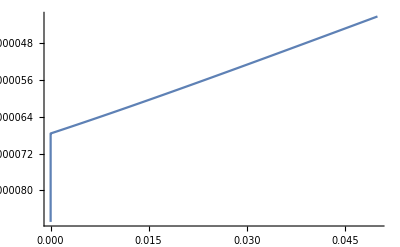

```mathematica
kt={1,0,0};
lt={1,-1,0};
mt={0,1,1};
nt={1/7 (1-2 √2+√(2 (29-2 √2))),0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]+myNorm[lt-nt]-(myNorm[mt]+myNorm[mt-nt])==0,a]*)
N[myNorm[kt]+myNorm[kt-lt]+myNorm[lt-nt]-(myNorm[mt]+myNorm[mt-nt]),12]

N[Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]],12]
N[r1CT72L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT72L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT52L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT52L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT72L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

```mathematica
r1CT71L[ks_,ls_,ms_,ns_]:=Log[((-myNorm[ls-ns]+myNorm[ms-ns]+myNorm[ms])^2-myNorm[ls]^2)/(2((-myNorm[ls-ns]+myNorm[ms-ns]+myNorm[ms])-ks.ls/myNorm[ks]))]

jacques1CT71L[ks_,ls_,ms_,ns_]:=(Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->r1CT71L[ks,ls,ms,ns]}
```

```mathematica
full1CT71L[ks_,ls_,ms_,ns_]:=(1/(jacques1CT71L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand1CT7[t*ks,ls,ms,ns]*subspaceThetaxSec1[t* ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r1CT71L[ks,ls,ms,ns]}
```

-0.69314718056

-0.69314718056

-0.00555198175775

0

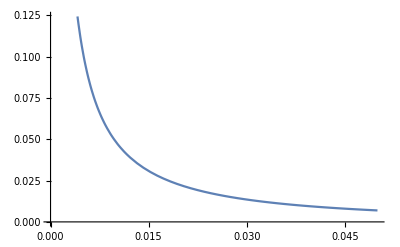

```mathematica
kt={1/2,0,0};
lt={1,-1,0};
mt={0,1,1};
nt={1/12 (1+2 √2+√5-2 √10+√(138-136 √2-38 √5+48 √10)),0,0};


N[Log[myNorm[kt]],12]
N[r1CT71L[kt,lt,mt,nt],12]

N[integrand1[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full1CT71L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(myNorm[lt]+myNorm[lt-mt]-(myNormMass[nt+eps{1,0,1/2}]+myNorm[mt-nt-eps{1,0,1/2}]))/(jacques1CT52L[kt,lt,mt,nt+eps{1,0,1/2}](Log[Sqrt[myNorm[kt]^2+myNorm[lt]^2]]-r1CT52L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand1[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full1CT71L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

## -Graphics-

#### Integrand

```mathematica
props2=prop[k,0]*prop[k-l,0]*prop[k+q,0]
diag2=cLTD[props2,loopmom->{k},EvalAll->True];
CForm[I*diag2[[1]]]
diag2[[2]]
integrand2[ks_,ls_,ms_,ns_]:=I*diag2[[1]]/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[k+q,0]

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

(-(1/((E0 + E1 + l(0))*(E0 + E2 - q(0)))) - 1/((E0 + E1 - l(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E1 - l(0))*(E0 + E2 + q(0))) - 
     1/((E0 + E1 + l(0))*(E1 + E2 + l(0) + q(0))) - 1/((E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))))/(8.*E0*E1*E2)

### -Graphics-

```mathematica
cLTD21=(-(1/((E0+E1+l[0])))-1/((E1+E2-l[0]-q[0])))/(8.*E0*E1*E2)
```

(0.125 (-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0])))/(E0 E1 E2)

```mathematica
integrand2CT1[ks_,ls_,ms_,ns_]:=cLTD21/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r2CT11L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ls]+myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns])/2]
jacques2CT11L[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r2CT11L[ks,ls,ms,ns]}
```

```mathematica
full2CT11L[ks_,ls_,ms_,ns_]:=(1/(jacques2CT11L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand2CT1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r2CT11L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3/2-2 √2-(√5)/2+√(1/2 (23+12 √2+3 √5+4 √10)).

0.

1.00181888023

1.00181888023

0.00105641086858

0.00330951

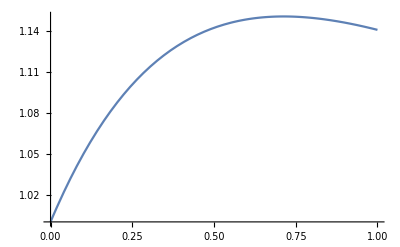

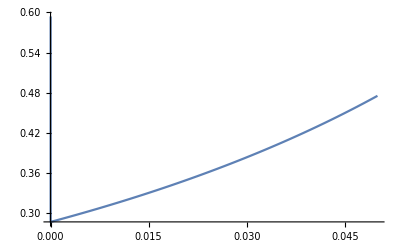

```mathematica
kt={1/2 √(1/2 (23+12 √2+3 √5+4 √10)),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[2*myNorm[kt]-(myNorm[lt]+myNorm[lt-mt]+myNorm[mt-nt]+myNormMass[nt])==0,a]*)

N[2*myNorm[kt]-(myNorm[lt]+myNorm[lt-mt]+myNorm[mt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r2CT11L[kt,lt,mt,nt],12]

N[integrand2[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full2CT11L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(2*myNorm[kt]-(myNorm[lt]+myNorm[lt-mt]+myNorm[mt-nt-eps{1,1,1/2}]+myNormMass[nt+eps{1,1,1/2}]))/(jacques2CT11L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r2CT11L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand2[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full2CT11L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

### -Graphics-

```mathematica
cLTD22=(-1/((E0+E1-l[0]))-1/((E0+E2-q[0])))/(8.*E0*E1*E2)
```

(0.125 (-1/(E0+E1-l[0])-1/(E0+E2-q[0])))/(E0 E1 E2)

```mathematica
integrand2CT2[ks_,ls_,ms_,ns_]:=cLTD22/.diag2[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ms]+myNorm[ms-ns]+myNormMass[ns],l[0]->-myNorm[ls]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r2CT21L[ks_,ls_,ms_,ns_]:=Log[((myNormMass[ns]+myNorm[ls-ms]+myNorm[ms-ns])^2-myNorm[ls]^2)/(2(myNormMass[ns]+myNorm[ls-ms]+myNorm[ms-ns]-ks.ls/myNorm[ks]))]
jacques2CT21L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[ls-Exp[r]ks/myNorm[ks]])/.{r->r2CT21L[ks,ls,ms,ns]}
```

```mathematica
full2CT21L[ks_,ls_,ms_,ns_]:=(1/(jacques2CT21L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand2CT2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r2CT21L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3/2-2 √2+3/31 (13+10 √2)+√(1/4+(-1+3/31 (13+Times[«2»]))^2).

0.

0.965712424651

0.965712424651

0.00144290135178

-0.00343175

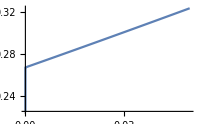

```mathematica
kt={3/31 (13+10 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-mt]+myNorm[mt-nt]+myNormMass[nt])==0,a]*)

N[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-mt]+myNorm[mt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r2CT21L[kt,lt,mt,nt],12]

N[integrand2[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full2CT21L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(2*myNorm[kt]-(myNorm[lt]+myNorm[lt-mt]+myNorm[mt-nt-eps{1,1,1/2}]+myNormMass[nt+eps{1,1,1/2}]))/(jacques2CT21L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r2CT21L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand2[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full2CT21L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

## -Graphics-

## -Graphics-

#### Integrand

```mathematica
props3L=prop[k,0]*prop[k-l,0]*prop[k+q,0]
diag3L=cLTD[props3L,loopmom->{k},EvalAll->True];
CForm[I*diag3L[[1]]]
diag3L[[2]]
integrand3L[ks_,ls_,ms_,ns_]:=I*diag3L[[1]]/.diag3L[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[k+q,0]

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

(-(1/((E0 + E1 + l(0))*(E0 + E2 - q(0)))) - 1/((E0 + E1 - l(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E1 - l(0))*(E0 + E2 + q(0))) - 
     1/((E0 + E1 + l(0))*(E1 + E2 + l(0) + q(0))) - 1/((E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))))/(8.*E0*E1*E2)

```mathematica
props3R=prop[m,0]*prop[m-l,0]*prop[m+q,0]*prop[m-n+q,0]
diag3R=cLTD[props3R,loopmom->{m},EvalAll->True];
CForm[I*diag3R[[1]]]
diag3R[[2]]
integrand3R[ks_,ls_,ms_,ns_]:=I*diag3R[[1]]/.diag3R[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[m,0] prop[-l+m,0] prop[m+q,0] prop[m-n+q,0]

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

(1/((E0 + E1 + l(0))*(E2 + E3 - n(0))*(E0 + E2 - q(0))) + 1/((E0 + E1 - l(0))*(E2 + E3 - n(0))*(E1 + E2 - l(0) - q(0))) + 1/((E2 + E3 - n(0))*(E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 + n(0))*(E0 + E3 + n(0) - q(0))) + 1/((E0 + E1 + l(0))*(E0 + E2 - q(0))*(E0 + E3 + n(0) - q(0))) + 
     1/((E0 + E1 - l(0))*(E2 + E3 + n(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E0 + E1 - l(0))*(E1 + E2 - l(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 
     1/((E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E2 + E3 + n(0))*(E0 + E3 + n(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 
     1/((E0 + E2 - q(0))*(E0 + E3 + n(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E0 + E1 - l(0))*(E2 + E3 + n(0))*(E0 + E2 + q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 + n(0))*(E1 + E2 + l(0) + q(0))) + 1/((E2 + E3 + n(0))*(E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))) + 
     1/((E0 + E1 - l(0))*(E2 + E3 - n(0))*(E0 + E3 - n(0) + q(0))) + 1/((E0 + E1 - l(0))*(E0 + E2 + q(0))*(E0 + E3 - n(0) + q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 - n(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 1/((E0 + E1 + l(0))*(E1 + E2 + l(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 
     1/((E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 1/((E2 + E3 - n(0))*(E0 + E3 - n(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 
     1/((E0 + E2 + q(0))*(E0 + E3 - n(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))))/(16.*E0*E1*E2*E3)

#### -Graphics-

```mathematica
cLTD31L=(-(1/((E0+E1+l[0])))-1/((E1+E2-l[0]-q[0])))/(8.*E0*E1*E2)
```

(0.125 (-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0])))/(E0 E1 E2)

```mathematica
integrand3CT1L[ks_,ls_,ms_,ns_]:=cLTD31L/.diag3L[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r3CT11LL[ks_,ls_,ms_,ns_]:=Log[(myNorm[ls]+myNorm[ls-ns]+myNormMass[ns])/2]
jacques3CT11LL[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r3CT11LL[ks,ls,ms,ns]}
```

```mathematica
full3CT11LL[ks_,ls_,ms_,ns_]:=(1/(jacques3CT11LL[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand3CT1L[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r3CT11LL[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2-(√5)/2+√(1/2 (7+2 √2+√5+2 √10)).

0.

0.416156930036

0.416156930036

0.0350496070166

0.0293305

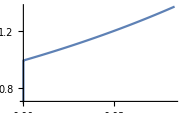

```mathematica
kt={1/2 √(1/2 (7+2 √2+√5+2 √10)),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[2*myNorm[kt]-(myNorm[lt]+myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[2*myNorm[kt]-(myNorm[lt]+myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r3CT11LL[kt,lt,mt,nt],12]

N[integrand3L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full3CT11LL[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
(*Plot[{(2*myNorm[kt]-(myNorm[lt]+myNorm[lt-mt]+myNorm[mt-nt-eps{1,1,1/2}]+myNormMass[nt+eps{1,1,1/2}]))/(jacques2CT11L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r2CT11L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]*)
Plot[{integrand3L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full3CT11LL[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

#### -Graphics-

```mathematica
cLTD32L=(-1/((E0+E1-l[0]))-1/((E0+E2-q[0])))/(8.*E0*E1*E2)
```

(0.125 (-1/(E0+E1-l[0])-1/(E0+E2-q[0])))/(E0 E1 E2)

```mathematica
integrand3CT2L[ks_,ls_,ms_,ns_]:=cLTD32L/.diag3L[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r3CT21LL[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ns]+myNormMass[ns])^2-myNorm[ls]^2)/(2(myNorm[ls-ns]+myNormMass[ns]-ks.ls/myNorm[ks]))]
jacques3CT21LL[ks_,ls_,ms_,ns_]:=(Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[Exp[r]*ks/myNorm[ks]-ls]))/.{r->r3CT21LL[ks,ls,ms,ns]}
```

```mathematica
full3CT21LL[ks_,ls_,ms_,ns_]:=(1/(jacques3CT21LL[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand3CT2L[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r3CT21LL[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2+1/7 (5+3 √2)+√(1/4+(-1+1/7 (5+Times[«2»]))^2).

0.

0.277917484418

0.277917484418

0.0631045068223

-0.0434539

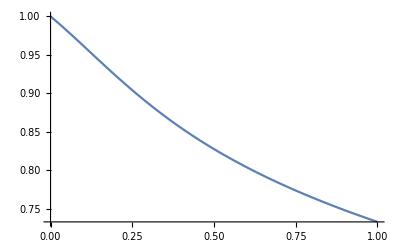

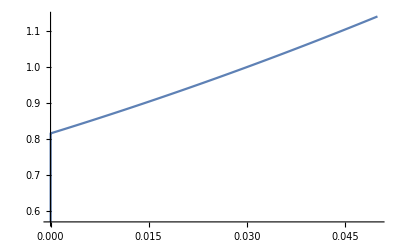

```mathematica
kt={1/7 (5+3 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r3CT21LL[kt,lt,mt,nt],12]

N[integrand3L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full3CT21LL[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques3CT21LL[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r3CT21LL[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand3L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full3CT21LL[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

#### -Graphics-

```mathematica
cLTD31R=(1/((E0+E1+l[0])*(E2+E3+n[0]))+1/((E0+E1+l[0])*(E0+E2-q[0]))+1/((E2+E3+n[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3)
```

(0.0625 (1/((E0+E1+l[0]) (E2+E3+n[0]))+1/((E0+E1+l[0]) (E0+E2-q[0]))+1/((E2+E3+n[0]) (E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0]) (E1+E3-l[0]+n[0]-q[0]))))/(E0 E1 E2 E3)

```mathematica
diag3R[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand3CT1R[ks_,ls_,ms_,ns_]:=cLTD31R/.diag3R[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r3CT11LR[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ns]+myNorm[ls])^2-myNorm[ns]^2)/(2(myNorm[ls-ns]+myNorm[ls]-ms.ns/myNorm[ms]))]
jacques3CT11LR[ks_,ls_,ms_,ns_]:=(Exp[r](1+(Exp[r]-ms.ns/myNorm[ms])/myNorm[Exp[r]*ms/myNorm[ms]-ns]))/.{r->r3CT11LR[ks,ls,ms,ns]}
```

```mathematica
full3CT11LR[ks_,ls_,ms_,ns_]:=(1/(jacques3CT11LR[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand3CT1R[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r3CT11LR[ks,ls,ms,ns]}
```

0

-0.69314718056

-0.69314718056

0.115336422454

0.0403081

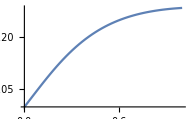

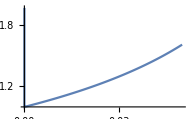

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/2};
nt={1,0,0};

(*Solve[myNorm[mt]+myNorm[mt-nt]-(myNorm[lt]+myNorm[lt-nt])==0,a]*)

N[myNorm[mt]+myNorm[mt-nt]-(myNorm[lt]+myNorm[lt-nt]),12]
N[Log[myNorm[mt]],12]
N[r3CT11LR[kt,lt,mt,nt],12]

N[integrand3L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full3CT11LR[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(myNorm[mt]+myNorm[mt-nt-eps{1,0,1/2}]-(myNorm[lt]+myNorm[lt-nt-eps{1,0,1/2}]))/(jacques3CT11LR[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r3CT11LR[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]

Plot[{integrand3R[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full3CT11LR[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

#### -Graphics-

```mathematica
cLTD23R=(1/((E0+E1+l[0])*(E2+E3-n[0]))+1/((E2+E3-n[0])*(E1+E2-l[0]-q[0]))+1/((E0+E1+l[0])*(E0+E3+n[0]-q[0]))+1/((E1+E2-l[0]-q[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E3+n[0]-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3);
```

```mathematica
diag3R[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand3CT2R[ks_,ls_,ms_,ns_]:=cLTD23R/.diag3R[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r3CT21LR[ks_,ls_,ms_,ns_]:=Log[(myNorm[ls-ns]+myNorm[ls]+myNormMass[ns])/2]
jacques3CT21LR[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r3CT21LR[ks,ls,ms,ns]}
```

```mathematica
full3CT21LR[ks_,ls_,ms_,ns_]:=(1/(jacques3CT21LR[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand3CT2R[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r3CT21LR[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2-(√5)/2+√(1/2 (7+2 √2+√5+2 √10)).

0.

0.416156930036

0.416156930036

-0.00336209171292

-0.000281382

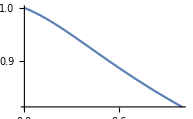

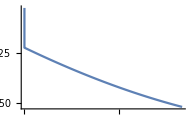

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/2 √(1/2 (7+2 √2+√5+2 √10))};
nt={1,0,0};

(*Solve[2*myNorm[mt]-(myNorm[lt]+myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[2*myNorm[mt]-(myNorm[lt]+myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[mt]],12]
N[r3CT21LR[kt,lt,mt,nt],12]

N[integrand3R[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full3CT21LR[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(2*myNorm[mt]-(myNorm[lt]+myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques3CT21LR[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r3CT21LR[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]

Plot[{integrand3R[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full3CT21LR[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

#### -Graphics-

```mathematica
cLTD24R=(1/((E0+E1-l[0])*(E2+E3-n[0]))+1/((E2+E3-n[0])*(E0+E2-q[0]))+1/((E0+E1-l[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3);
```

```mathematica
diag3R[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand3CT3R[ks_,ls_,ms_,ns_]:=cLTD24R/.diag3R[[2]]/.{q[0]->myNorm[ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->-myNorm[ls],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r3CT31LR[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ns]+myNormMass[ns])^2-myNorm[ls]^2)/(2(myNorm[ls-ns]+myNormMass[ns]-ms.ls/myNorm[ms]))]
jacques3CT31LR[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ls.ms/myNorm[ms])/myNorm[Exp[r]ms/myNorm[ms]-ls])/.{r->r3CT31LR[ks,ls,ms,ns]}
```

```mathematica
full3CT31LR[ks_,ls_,ms_,ns_]:=(1/(jacques3CT31LR[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand3CT3R[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r3CT31LR[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2+1/7 √(11+6 √2)+√(5/4+1/49 (11+6 √2)).

0.

-0.461080459434

-0.461080459434

-0.311531767743

0.0605223

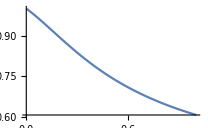

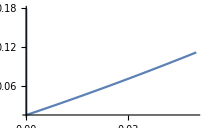

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/7 √(11+6 √2)};
nt={1,0,0};

(*Solve[myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[mt]],12]
N[r3CT31LR[kt,lt,mt,nt],12]

N[integrand3R[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full3CT31LR[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques3CT31LR[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r3CT31LR[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]

Plot[{integrand3R[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full3CT31LR[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

## -Graphics-

```mathematica
props4=prop[k,0]*prop[k-l,0]*prop[k+q,0]
diag4=cLTD[props4,loopmom->{k},EvalAll->True];
CForm[I*diag4[[1]]]
diag4[[1]]
integrand4[ks_,ls_,ms_,ns_]:=I*diag4[[1]]/.diag4[[2]]/.{q[0]->myNorm[ms]+myNorm[ms-ls]+myNorm[ls-ns]+myNormMass[ns],l[0]-> m[0]-myNorm[ms-ls]}/.{m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[k,0] prop[k-l,0] prop[k+q,0]

-(ⅈ (-1/((E0+E1+l[0]) (E0+E2-q[0]))-1/((E0+E1-l[0]) (E1+E2-l[0]-q[0]))-1/((E0+E2-q[0]) (E1+E2-l[0]-q[0]))-1/((E0+E1-l[0]) (E0+E2+q[0]))-1/((E0+E1+l[0]) (E1+E2+l[0]+q[0]))-1/((E0+E2+q[0]) (E1+E2+l[0]+q[0]))))/(8 E0 E1 E2)

(-(1/((E0 + E1 + l(0))*(E0 + E2 - q(0)))) - 1/((E0 + E1 - l(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))) - 1/((E0 + E1 - l(0))*(E0 + E2 + q(0))) - 
     1/((E0 + E1 + l(0))*(E1 + E2 + l(0) + q(0))) - 1/((E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))))/(8.*E0*E1*E2)

#### -Graphics-

```mathematica
cLTD41=(-(1/((E0+E1+l[0])))-1/((E1+E2-l[0]-q[0])))/(8.*E0*E1*E2)
```

(0.125 (-1/(E0+E1+l[0])-1/(E1+E2-l[0]-q[0])))/(E0 E1 E2)

```mathematica
diag4[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

```mathematica
integrand4CT1[ks_,ls_,ms_,ns_]:=cLTD41/.diag4[[2]]/.{q[0]->myNorm[ms]+myNorm[ms-ls]+myNorm[ls-ns]+myNormMass[ns],l[0]-> m[0]-myNorm[ms-ls]}/.{m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r4CT11L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ms]+myNorm[ms-ls]+myNorm[ls-ns]+myNormMass[ns])/2]
jacques4CT11L[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r4CT11L[ks,ls,ms,ns]}
```

```mathematica
full4CT11L[ks_,ls_,ms_,ns_]:=(1/(jacques4CT11L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand4CT1[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r4CT11L[ks,ls,ms,ns]}
```

0

0.791682509061

0.791682509061

0.0167271482765

0.0119325

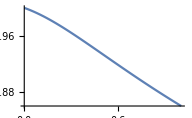

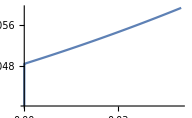

```mathematica
kt={1/2 (3+√2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[2*myNorm[kt]-(myNorm[mt]+myNorm[mt-lt]+myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[2*myNorm[kt]-(myNorm[mt]+myNorm[mt-lt]+myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r4CT11L[kt,lt,mt,nt],12]

N[integrand4[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full4CT11L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
Plot[{(2*myNorm[kt]-(myNorm[mt]+myNorm[mt-lt]+myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques4CT11L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r4CT11L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand4[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full4CT11L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.05}]
```

#### -Graphics-

```mathematica
cLTD42=(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)
```

(-1/(E0+E1-l[0])-1/(E0+E2-q[0]))/(8 E0 E1 E2)

```mathematica
diag4[[2]]
```

{E0→√(k.k),E1→√(k.k-2 k.l+l.l),E2→√(k.k+2 k.q+q.q)}

```mathematica
integrand4CT2[ks_,ls_,ms_,ns_]:=cLTD42/.diag4[[2]]/.{q[0]->myNorm[ms]+myNorm[ms-ls]+myNorm[ls-ns]+myNormMass[ns],l[0]-> m[0]-myNorm[ms-ls]}/.{m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r4CT21L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ns]+myNormMass[ns])^2-myNorm[ls]^2)/(2((myNorm[ls-ns]+myNormMass[ns])-ks.ls/myNorm[ks]))]
jacques4CT21L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[ls-Exp[r]ks/myNorm[ks]])/.{r->r4CT21L[ks,ls,ms,ns]}
```

```mathematica
full4CT21L[ks_,ls_,ms_,ns_]:=(1/(jacques4CT21L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand4CT2[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r4CT21L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2+1/7 (5+3 √2)+√(1/4+(-1+1/7 (5+Times[«2»]))^2).

0.

0.277917484418

0.277917484418

-0.0310736386683

-0.0155110663453

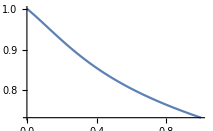

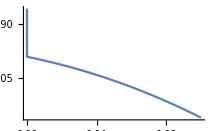

```mathematica
kt={1/7 (5+3 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[kt]],12]
N[r4CT21L[kt,lt,mt,nt],12]

N[integrand4[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full4CT21L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques4CT21L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[kt]]-r4CT21L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]

Plot[{integrand4[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full4CT21L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

#### -Graphics-

```mathematica
cLTD43=(-1/(E0+E2-q[0])-1/(E1+E2+l[0]+q[0]))/(8 E0 E1 E2)
```

(-1/(E0+E2-q[0])-1/(E1+E2+l[0]+q[0]))/(8 E0 E1 E2)

```mathematica
integrand4CT3[ks_,ls_,ms_,ns_]:=cLTD43/.diag4[[2]]/.{q[0]->myNorm[ms]+myNorm[ms-ls]+myNorm[ls-ns]+myNormMass[ns],l[0]-> m[0]-myNorm[ms-ls]}/.{m[0]->-myNorm[ms],n[0]->myNormMass[ns]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r4CT31L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ms]+myNorm[ms])^2-myNorm[ls]^2)/(2((myNorm[ls-ms]+myNorm[ms])-ks.ls/myNorm[ks]))]
jacques4CT31L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ks.ls/myNorm[ks])/myNorm[ls-Exp[r]ks/myNorm[ks]])/.{r->r4CT31L[ks,ls,ms,ns]}
```

```mathematica
full4CT31L[ks_,ls_,ms_,ns_]:=(1/(jacques4CT31L[ks,ls,ms,ns](Log[myNorm[ks]]-r))*integrand4CT3[t*ks,ls,ms,ns])/.{t->Exp[r]/myNorm[ks]}/.{r->r4CT31L[ks,ls,ms,ns]}
```

0

0.510825623766

0.510825623766

-0.0540927209114

-0.0164836413227

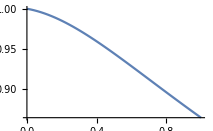

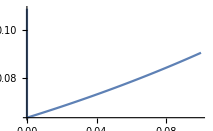

```mathematica
kt={5/3,0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};

(*Solve[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-mt]+myNorm[mt])==0,a]*)

N[myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-mt]+myNorm[mt]),12]
N[Log[myNorm[kt]],12]
N[r4CT31L[kt,lt,mt,nt],12]

N[integrand4[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full4CT31L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(myNorm[kt]+myNorm[kt-lt]-(myNorm[lt-mt-eps{1,0,1/2}]+myNorm[mt+eps{1,0,1/2}]))/(jacques4CT31L[kt,lt,mt+eps{1,0,1/2},nt](Log[myNorm[kt]]-r4CT31L[kt,lt,mt+eps{1,0,1/2},nt]))},{eps,0,1}]

Plot[{integrand4[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full4CT31L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

## -Graphics-

```mathematica
props5=prop[m,0]*prop[m-l,0]*prop[m+q,0]*prop[m-n+q,0]
diag5=cLTD[props5,loopmom->{m},EvalAll->True];
CForm[I*diag5[[1]]]
diag5[[2]]
integrand5[ks_,ls_,ms_,ns_]:=I*diag5[[1]]/.diag5[[2]]/.{q[0]->myNorm[ks]+myNorm[ks-ls]+myNorm[ls-ns]+myNormMass[ns],l[0]->k[0]-myNorm[ks-ls],n[0]->myNormMass[ns]}/.{k[0]->-myNorm[ks]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

prop[m,0] prop[-l+m,0] prop[m+q,0] prop[m-n+q,0]

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

(1/((E0 + E1 + l(0))*(E2 + E3 - n(0))*(E0 + E2 - q(0))) + 1/((E0 + E1 - l(0))*(E2 + E3 - n(0))*(E1 + E2 - l(0) - q(0))) + 1/((E2 + E3 - n(0))*(E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 + n(0))*(E0 + E3 + n(0) - q(0))) + 1/((E0 + E1 + l(0))*(E0 + E2 - q(0))*(E0 + E3 + n(0) - q(0))) + 
     1/((E0 + E1 - l(0))*(E2 + E3 + n(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E0 + E1 - l(0))*(E1 + E2 - l(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 
     1/((E0 + E2 - q(0))*(E1 + E2 - l(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E2 + E3 + n(0))*(E0 + E3 + n(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 
     1/((E0 + E2 - q(0))*(E0 + E3 + n(0) - q(0))*(E1 + E3 - l(0) + n(0) - q(0))) + 1/((E0 + E1 - l(0))*(E2 + E3 + n(0))*(E0 + E2 + q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 + n(0))*(E1 + E2 + l(0) + q(0))) + 1/((E2 + E3 + n(0))*(E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))) + 
     1/((E0 + E1 - l(0))*(E2 + E3 - n(0))*(E0 + E3 - n(0) + q(0))) + 1/((E0 + E1 - l(0))*(E0 + E2 + q(0))*(E0 + E3 - n(0) + q(0))) + 
     1/((E0 + E1 + l(0))*(E2 + E3 - n(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 1/((E0 + E1 + l(0))*(E1 + E2 + l(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 
     1/((E0 + E2 + q(0))*(E1 + E2 + l(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 1/((E2 + E3 - n(0))*(E0 + E3 - n(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))) + 
     1/((E0 + E2 + q(0))*(E0 + E3 - n(0) + q(0))*(E1 + E3 + l(0) - n(0) + q(0))))/(16.*E0*E1*E2*E3)

#### -Graphics-

```mathematica
cLTD51=(1/((E0+E1+l[0])*(E2+E3-n[0]))+1/((E2+E3-n[0])*(E1+E2-l[0]-q[0]))+1/((E0+E1+l[0])*(E0+E3+n[0]-q[0]))+1/((E1+E2-l[0]-q[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E3+n[0]-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3);
```

```mathematica
integrand5CT1[ks_,ls_,ms_,ns_]:=cLTD51/.diag5[[2]]/.{q[0]->myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns]+myNormMass[ns],l[0]->k[0]-myNorm[ks-ls],n[0]->myNormMass[ns]}/.{k[0]->-myNorm[ks]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r5CT11L[ks_,ls_,ms_,ns_]:=Log[(myNorm[ks]+myNorm[ks-ls]+myNorm[ls-ns]+myNormMass[ns])/2]
jacques5CT11L[ks_,ls_,ms_,ns_]:=2*Exp[r]/.{r->r5CT11L[ks,ls,ms,ns]}
```

```mathematica
full5CT11L[ks_,ls_,ms_,ns_]:=(1/(jacques5CT11L[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand5CT1[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r5CT11L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1-1/(√2)-√2+1/2 (2+3 √2).

0.

0.445108918781

0.445108918781

-0.00306751864117

-0.000282488

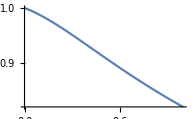

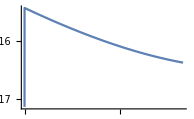

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/4 (2+3 √2)};
nt={1,0,0};

(*Solve[2*myNorm[mt]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[2*myNorm[mt]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[mt]],12]
N[r5CT11L[kt,lt,mt,nt],12]

N[integrand5[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full5CT11L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(2*myNorm[mt]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques5CT11L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r5CT11L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand5[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full5CT11L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

#### -Graphics-

```mathematica
cLTD52=(1/((E0+E1-l[0])*(E2+E3-n[0]))+1/((E2+E3-n[0])*(E0+E2-q[0]))+1/((E0+E1-l[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3)
```

(0.0625 (1/((E0+E1-l[0]) (E2+E3-n[0]))+1/((E2+E3-n[0]) (E0+E2-q[0]))+1/((E0+E1-l[0]) (E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0]) (E1+E3-l[0]+n[0]-q[0]))))/(E0 E1 E2 E3)

```mathematica
diag5[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand5CT2[ks_,ls_,ms_,ns_]:=cLTD52/.diag5[[2]]/.{q[0]->myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns]+myNormMass[ns],l[0]->k[0]-myNorm[ks-ls],n[0]->myNormMass[ns]}/.{k[0]->-myNorm[ks]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r5CT21L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ls-ns]+myNormMass[ns])^2-myNorm[ls]^2)/(2(myNorm[ls-ns]+myNormMass[ns]-ms.ls/myNorm[ms]))]
jacques5CT21L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ls.ms/myNorm[ms])/myNorm[ls-Exp[r]ms/myNorm[ms]])/.{r->r5CT21L[ks,ls,ms,ns]}
```

```mathematica
full5CT21L[ks_,ls_,ms_,ns_]:=(1/(jacques5CT21L[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand5CT2[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r5CT21L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-√2+1/7 √(11+6 √2)+√(5/4+1/49 (11+6 √2)).

0.

-0.461080459434

-0.461080459434

0.324127052307

0.0594374

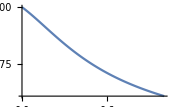

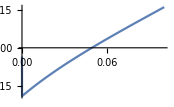

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/7 √(11+6 √2)};
nt={1,0,0};

(*Solve[myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt]+myNormMass[nt])==0,a]*)

N[myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt]+myNormMass[nt]),12]
N[Log[myNorm[mt]],12]
N[r5CT21L[kt,lt,mt,nt],12]

N[integrand5[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full5CT21L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(myNorm[mt]+myNorm[mt-lt]-(myNorm[lt-nt-eps{1,0,1/2}]+myNormMass[nt+eps{1,0,1/2}]))/(jacques5CT21L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r5CT21L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]
Plot[{integrand5[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full5CT21L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

#### -Graphics-

```mathematica
cLTD53=(1/((E0+E1+l[0])*(E2+E3+n[0]))+1/((E0+E1+l[0])*(E0+E2-q[0]))+1/((E2+E3+n[0])*(E1+E3-l[0]+n[0]-q[0]))+1/((E0+E2-q[0])*(E1+E3-l[0]+n[0]-q[0])))/(16.*E0*E1*E2*E3);
```

```mathematica
diag5[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand5CT3[ks_,ls_,ms_,ns_]:=cLTD53/.diag5[[2]]/.{q[0]->myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns]+myNormMass[ns],l[0]->k[0]-myNorm[ks-ls],n[0]->myNormMass[ns]}/.{k[0]->-myNorm[ks]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r5CT31L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns])^2-myNorm[ns]^2)/(2(myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns]-ms.ns/myNorm[ms]))]
jacques5CT31L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ns.ms/myNorm[ms])/myNorm[ns-Exp[r]ms/myNorm[ms]])/.{r->r5CT31L[ks,ls,ms,ns]}
```

```mathematica
full5CT31L[ks_,ls_,ms_,ns_]:=(1/(jacques5CT31L[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand5CT3[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r5CT31L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-1/(√2)-(√5)/2+1/12 (14-4 √2+4 √5-4 √10+√(2 (192-115 Power[«2»]+85 Power[«2»]-51 Power[«2»])))+√(1+(-1+1/12 (14+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]))^2).

0.

0.25095479349

0.25095479349

-0.0507043653519

-0.0591044

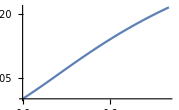

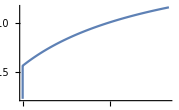

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/12 (14-4 √2+4 √5-4 √10+√(2 (192-115 √2+85 √5-51 √10)))};
nt={1,0,1};

(*Solve[myNorm[mt]+myNorm[mt-nt]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt])==0,a]*)

N[myNorm[mt]+myNorm[mt-nt]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt]),12]
N[Log[myNorm[mt]],12]
N[r5CT31L[kt,lt,mt,nt],12]

N[integrand5[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full5CT31L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(myNorm[mt]+myNorm[mt-nt-eps{1,0,1/2}]-(myNorm[kt]+myNorm[lt-kt]+myNorm[lt-nt-eps{1,0,1/2}]))/(jacques5CT31L[kt,lt,mt,nt+eps{1,0,1/2}](Log[myNorm[mt]]-r5CT31L[kt,lt,mt,nt+eps{1,0,1/2}]))},{eps,0,1}]

Plot[{integrand5[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]-full5CT31L[kt,lt+eps{1,1,1/2},mt+eps{1,1,1/2},nt]},{eps,0,0.1}]
```

#### -Graphics-

```mathematica
cLTD54=(1/((E2+E3-n[0])*(E0+E2-q[0]))+1/((E2+E3+n[0])*(E0+E3+n[0]-q[0]))+1/((E0+E2-q[0])*(E0+E3+n[0]-q[0]))+1/((E2+E3+n[0])*(E1+E2+l[0]+q[0]))+1/((E2+E3-n[0])*(E1+E3+l[0]-n[0]+q[0]))+1/((E1+E2+l[0]+q[0])*(E1+E3+l[0]-n[0]+q[0])))/(16.*E0*E1*E2*E3);
```

```mathematica
diag5[[2]]
```

{E0→√(m.m),E1→√(l.l-2 l.m+m.m),E2→√(m.m+2 m.q+q.q),E3→√(m.m-2 m.n+2 m.q+n.n-2 n.q+q.q)}

```mathematica
integrand5CT4[ks_,ls_,ms_,ns_]:=cLTD54/.diag5[[2]]/.{q[0]->myNorm[ks]+myNorm[ls-ks]+myNorm[ls-ns]+myNormMass[ns],l[0]->k[0]-myNorm[ks-ls],n[0]->myNormMass[ns]}/.{k[0]->-myNorm[ks]}/.{k->{ks[[1]],ks[[2]],ks[[3]]},l->{ls[[1]],ls[[2]],ls[[3]]},m->{ms[[1]],ms[[2]],ms[[3]]},n->{ns[[1]],ns[[2]],ns[[3]]},q->{0,0,0}}
```

```mathematica
r5CT41L[ks_,ls_,ms_,ns_]:=Log[((myNorm[ks]+myNorm[ls-ks])^2-myNorm[ls]^2)/(2(myNorm[ks]+myNorm[ls-ks]-ms.ls/myNorm[ms]))]
jacques5CT41L[ks_,ls_,ms_,ns_]:=Exp[r](1+(Exp[r]-ls.ms/myNorm[ms])/myNorm[ls-Exp[r]ms/myNorm[ms]])/.{r->r5CT41L[ks,ls,ms,ns]}
```

```mathematica
full5CT41L[ks_,ls_,ms_,ns_]:=(1/(jacques5CT41L[ks,ls,ms,ns](Log[myNorm[ms]]-r))*integrand5CT4[ks,ls,t*ms,ns])/.{t->Exp[r]/myNorm[ms]}/.{r->r5CT41L[ks,ls,ms,ns]}
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/2-1/(√2)+1/2 √(17-12 √2)+√(5/4+1/4 (17-12 √2)).

0.

-2.4558943546

-2.4558943546

0.297101984774

0.746113

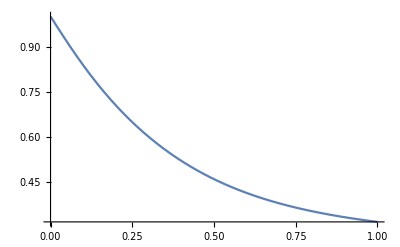

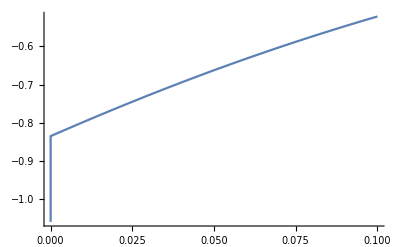

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/2 √(17-12 √2)};
nt={1,0,1};

(*Solve[myNorm[mt]+myNorm[mt-lt]-(myNorm[kt]+myNorm[lt-kt])==0,a]*)

N[myNorm[mt]+myNorm[mt-lt]-(myNorm[kt]+myNorm[lt-kt]),12]
N[Log[myNorm[mt]],12]
N[r5CT41L[kt,lt,mt,nt],12]

N[integrand5[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]
N[full5CT41L[kt,lt+{1,0,1/2},mt,nt+{1,0,1/2}],12]

Plot[{(myNorm[mt]+myNorm[mt-lt]-(myNorm[kt+eps{1,0,1/2}]+myNorm[lt-kt-eps{1,0,1/2}]))/(jacques5CT41L[kt+eps{1,0,1/2},lt,mt,nt](Log[myNorm[mt]]-r5CT41L[kt+eps{1,0,1/2},lt,mt,nt]))},{eps,0,1}]

Plot[{integrand5[kt+eps{1,0,1/2},lt,mt,nt]-full5CT41L[kt+eps{1,0,1/2},lt,mt,nt]},{eps,0,0.1}]
```

## Assembling the integrand

-Graphics-

```mathematica
xSec1[ks_,ls_,ms_,ns_]:=1/(8myNorm[ms]myNorm[ms-ns]myNormMass[ns])1/MS[{myNormMass[ns]+myNorm[ns-ms],ms[[1]],ms[[2]],ms[[3]]}](integrand1[ks,ls,ms,ns]-(*notsubspaceThetaxSec1[ks,ls,ms,ns]*)(full1CT12L[ks,ls,ms,ns]+full1CT22L[ks,ls,ms,ns]+full1CT32L[ks,ls,ms,ns]+0*full1CT42L[ks,ls,ms,ns]+full1CT52L[ks,ls,ms,ns]+full1CT62L[ks,ls,ms,ns]+0*full1CT72L[ks,ls,ms,ns])-(*subspaceThetaxSec1[ks,ls,ms,ns]*)(full1CT11L[ks,ls,ms,ns]+full1CT21L[ks,ls,ms,ns]+full1CT61L[ks,ls,ms,ns]+0*full1CT71L[ks,ls,ms,ns]))
```

-Graphics-

```mathematica
xSec2[ks_,ls_,ms_,ns_]:=1/(16 myNorm[ls]myNorm[ms-ls]myNorm[ms-ns]myNormMass[ns])1/MS[{myNorm[ls]+myNorm[ls-ms],ms[[1]],ms[[2]],ms[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ms],ms[[1]],ms[[2]],ms[[3]]}]1/MS[{myNorm[ls-ms]+myNorm[ns-ms],ls[[1]]-ns[[1]],ls[[2]]-ns[[2]],ls[[3]]-ns[[3]]}]1/MS[{myNorm[ls-ms]+myNorm[ns-ms]+myNormMass[ns],ls[[1]],ls[[2]],ls[[3]]}](integrand2[ks,ls,ms,ns] - (full2CT11L[ks,ls,ms,ns]+full2CT21L[ks,ls,ms,ns]))
```

-Graphics-

```mathematica
xSec3[ks_,ls_,ms_,ns_]:=-1/(32 myNorm[ks]myNorm[ks-ls]myNorm[ms-ls]myNorm[ms-ns]myNormMass[ns])1/MS[{myNorm[ks]+myNorm[ks-ls],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNorm[ks]+myNorm[ks-ls]+myNorm[ls-ms],ms[[1]],ms[[2]],ms[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ms],ms[[1]],ms[[2]],ms[[3]]}]1/MS[{myNorm[ls-ms]+myNorm[ns-ms],ls[[1]]-ns[[1]],ls[[2]]-ns[[2]],ls[[3]]-ns[[3]]}]1/MS[{myNorm[ls-ms]+myNorm[ns-ms]+myNormMass[ns],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNorm[ks-ls]+myNorm[ls-ms]+myNorm[ns-ms]+myNormMass[ns],ks[[1]],ks[[2]],ks[[3]]}]
```

-Graphics-

```mathematica
xSec4[ks_,ls_,ms_,ns_]:=-1/(8myNorm[ls]myNorm[ls-ns]myNormMass[ns])1/MS[{myNormMass[ns]+myNorm[ns-ls],ls[[1]],ls[[2]],ls[[3]]}](integrand3L[ks,ls,ms,ns]-(full3CT11LL[ks,ls,ms,ns]+full3CT21LL[ks,ls,ms,ns]))(integrand3R[ks,ls,ms,ns]-(0*full3CT11LR[ks,ls,ms,ns]+full3CT21LR[ks,ls,ms,ns]+full3CT31LR[ks,ls,ms,ns]))
```

-Graphics-

```mathematica
xSec5[ks_,ls_,ms_,ns_]:=1/(16myNorm[ms]myNorm[ls-ms]myNorm[ls-ns]myNormMass[ns])1/MS[{myNorm[ms]+myNorm[ms-ls],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNorm[ls-ns]+myNorm[ms-ls],ms[[1]]-ns[[1]],ms[[2]]-ns[[2]],ms[[3]]-ns[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ls],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ls]+myNorm[ls-ms],ms[[1]],ms[[2]],ms[[3]]}](integrand4[ks,ls,ms,ns]-(full4CT11L[ks,ls,ms,ns]+full4CT21L[ks,ls,ms,ns]+0*full4CT31L[ks,ls,ms,ns]))
```

-Graphics-

```mathematica
xSec6[ks_,ls_,ms_,ns_]:=1/(16myNorm[ks]myNorm[ls-ks]myNorm[ls-ns]myNormMass[ns])1/MS[{myNorm[ks]+myNorm[ks-ls],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ls],ls[[1]],ls[[2]],ls[[3]]}]1/MS[{myNormMass[ns]+myNorm[ns-ls]+myNorm[ls-ks],ks[[1]],ks[[2]],ks[[3]]}](integrand5[ks,ls,ms,ns]-(full5CT11L[ks,ls,ms,ns]+full5CT21L[ks,ls,ms,ns]+0*full5CT31L[ks,ls,ms,ns]+0*full5CT41L[ks,ls,ms,ns]))
```

```mathematica
totxSec[ks_,ls_,ms_,ns_]:=xSec1[ks,ls,ms,ns]+xSec2[ks,ls,ms,ns]+xSec3[ks,ls,ms,ns]+xSec4[ks,ls,ms,ns]+xSec5[ks,ls,ms,ns]+xSec6[ks,ls,ms,ns]
```

## Tests

### Collinear

-Graphics-

7.70114×10^-8

1.02626×10^-7

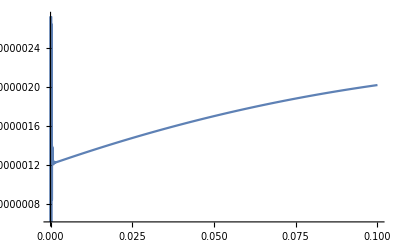

```mathematica
kt={1,1,1};
lt={0,0,0.3};
mt={0,0,1};
nt={1,0,1};
xSec1[kt,lt,mt+{0,1,1},nt]
xSec2[kt,lt,mt+{0,1,1},nt]
Plot[{totxSec[kt,lt,mt+eps{0,1,1},nt]},{eps,0,0.1}]
(*Plot[{xSec1[kt,lt,mt+eps{0,1,1},nt]+xSec2[kt,lt,mt+eps{0,1,1},nt],xSec3[kt,lt,mt+eps{0,1,1},nt],xSec4[kt,lt,mt+eps{0,1,1},nt],xSec5[kt,lt,mt+eps{0,1,1},nt],xSec6[kt,lt,mt+eps{0,1,1},nt]*)(*full3CT11LR[kt,lt,mt+eps{0,1,1},nt],full1CT42L[kt,lt,mt+eps{0,1,1},nt]*)(*,full3CT21LR[kt,lt,mt+eps{0,1,1},nt]+full3CT31LR[kt,lt,mt+eps{0,1,1},nt]},{eps,0,0.1}]*)
```

-Graphics-

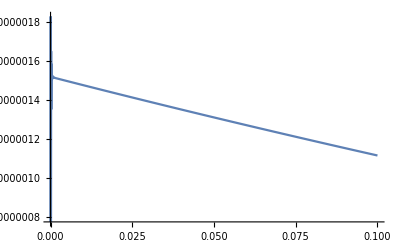

```mathematica
kt={1,1,1};
lt={0,0.5,1};
mt={-0.3,0.5,1};
nt={1,0.5,1};

Plot[{totxSec[kt,lt,mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

-Graphics-

```mathematica
kt={1,1,1};
lt={0,0,1};
mt={0,0,0.3};
nt={1,0,1};
```

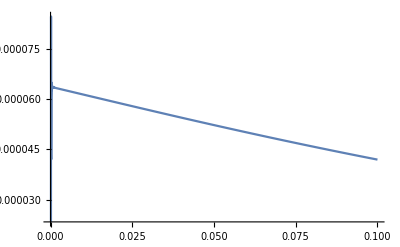

```mathematica
Plot[{totxSec[kt,lt,mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

```mathematica
kt={1,1,1};
lt={0,0.5,1};
mt={0.3,0.5,1};
nt={1,0.5,1};
```

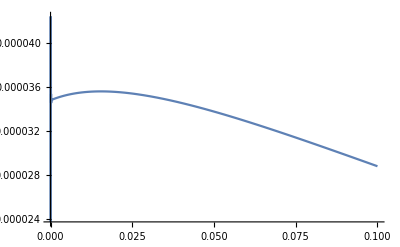

```mathematica
Plot[{totxSec[kt,lt,mt+eps{0,1,1},nt]},{eps,0,0.1}]
```

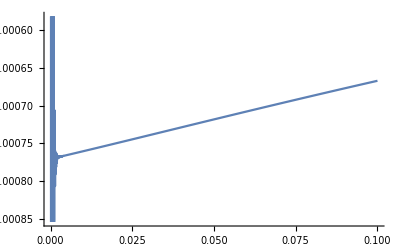

```mathematica
kt={0,0,0.3};
lt={0,0,1};
mt={0.3,0.2,1};
nt={1,0.5,1};

Plot[{totxSec[kt+eps{0,1,1},lt,mt,nt]},{eps,0,0.1}]
```

-Graphics-

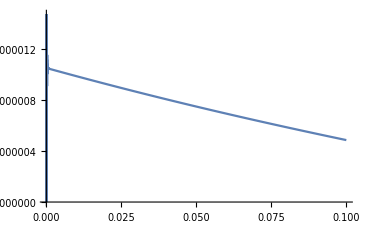

```mathematica
kt={0.5,0,0.3};
lt={0,0,1};
mt={0,0,1};
nt={1,0.5,1};

Plot[{eps totxSec[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

-Graphics-

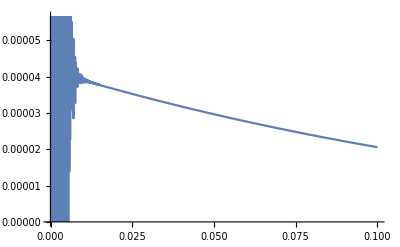

```mathematica
mt={0,0,1};
lt={0,0,1};
kt={0,0,0.3};
nt={1,0.5,1};
Plot[{eps totxSec[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

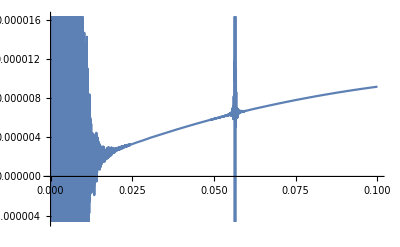

```mathematica
kt={0,0,0.3};
lt={0,0,1};
mt={0,0,0.5};
nt={1,0.5,1};
Plot[{eps totxSec[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

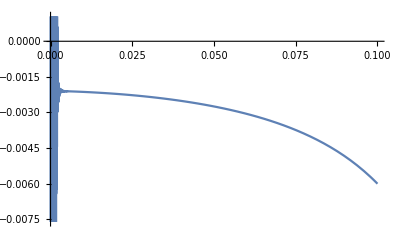

```mathematica
mt={0,0,1};
lt={0,0,0.5};
kt={0,0,0.3};
nt={1,0.5,1};
Plot[{totxSec[kt,lt+eps{0,1,1},mt,nt]},{eps,0,0.1}]
```

### Threshold

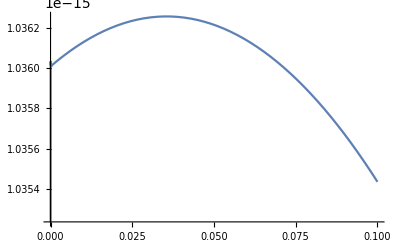

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={4+√10,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{0,1,1}]},{eps,0,0.1}]
```

-1.13901×10^-6+0. ⅈ

-0.00460297

0.+0. ⅈ

0.325151+3.14159 ⅈ

-0.26217-1.50157×10^-17 ⅈ

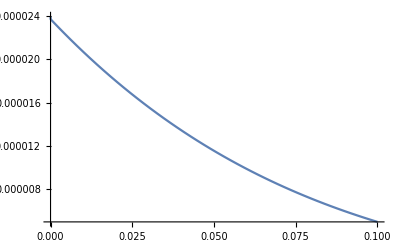

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/14 √(15/2 (79-52 √2)),0,0};
xSec1[kt,lt,mt,nt+0.05{1,1,1}]
integrand1[kt,lt,mt,nt+0.05{1,1,1}]

full1CT61L[kt,lt,mt,nt+0.05{1,1,1}]
r1CT61L[kt,lt,mt,nt+0.05{1,1,1}]
jacques1CT61L[kt,lt,mt,nt+0.05{1,1,1}]
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

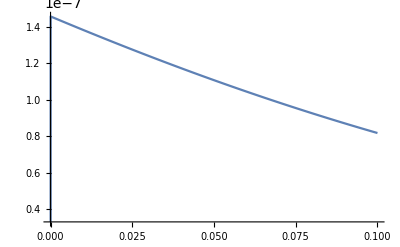

```mathematica
kt={2,0,0};
lt={0,-1,0};
mt={0,1,1};
nt={1/6 √(1/2 (192-101 √2+103 √5-39 √10)),0,0};

Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

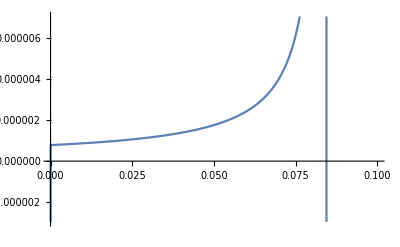

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/18 √(19/2 (137-34 √10)),0,0};

Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

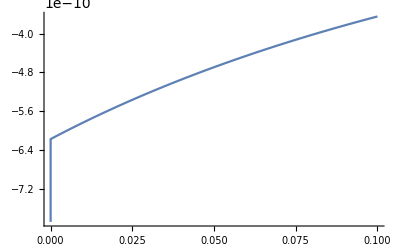

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/6 √(1/2 (188+35 √55)),0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

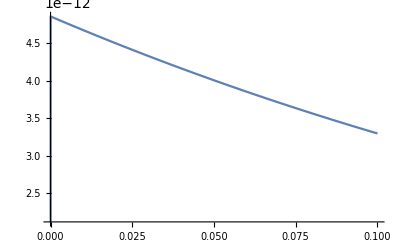

```mathematica
kt={2,0,0};
lt={1,-2,0};
mt={0,1,1};
nt={1/38 √(1/2 (10358+2970 √5+2826 √11+1415 √55)),0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

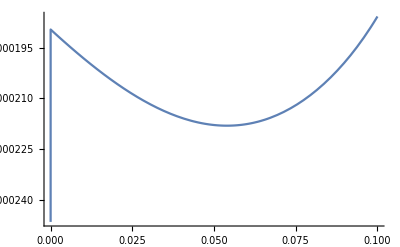

```mathematica
kt={1/2,0,0};
lt={1,-1,0};
mt={0,1,1};
nt={1/12 (1+2 √2+√5-2 √10+√(138-136 √2-38 √5+48 √10)),0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

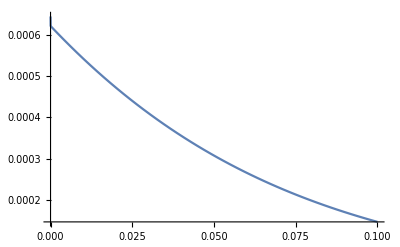

```mathematica
kt={1/2 √(1/2 (23+12 √2+3 √5+4 √10)),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

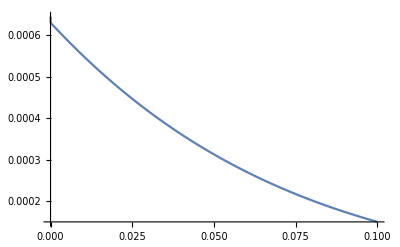

```mathematica
kt={3/31 (13+10 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

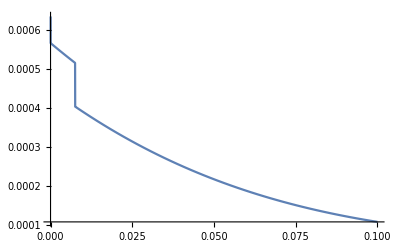

```mathematica
kt={1/2 √(1/2 (7+2 √2+√5+2 √10)),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

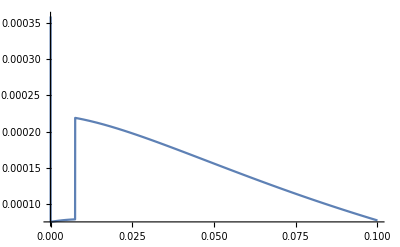

```mathematica
kt={1/7 (5+3 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

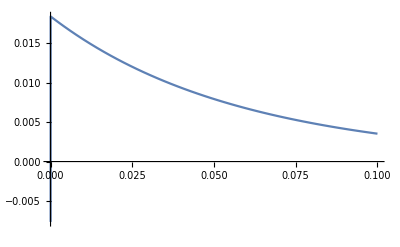

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/2};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

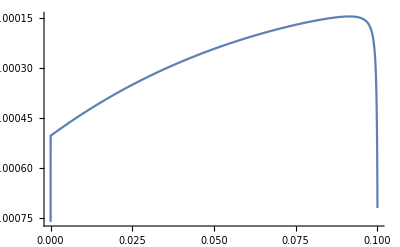

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/2 √(1/2 (7+2 √2+√5+2 √10))};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

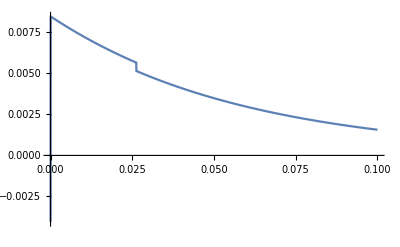

```mathematica
kt={1,0,0};
lt={1,-1/2,0};
mt={0,0,1/7 √(11+6 √2)};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

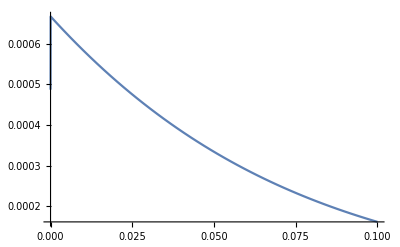

```mathematica
kt={1/2 (3+√2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

```mathematica
kt={1/7 (5+3 √2),0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

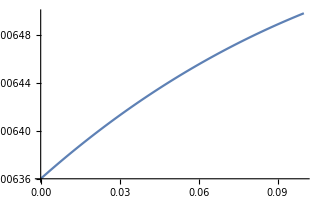

```mathematica
kt={5/3,0,0};
lt={1,-1/2,0};
mt={0,0,1};
nt={1,0,0};
Plot[{totxSec[kt+eps{1,1,1},lt,mt,nt]},{eps,0,0.1}]
```

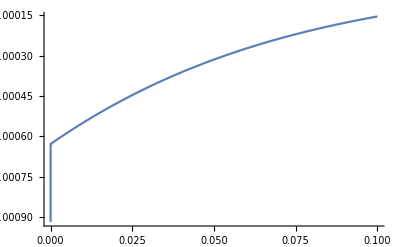

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/4 (2+3 √2)};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics-

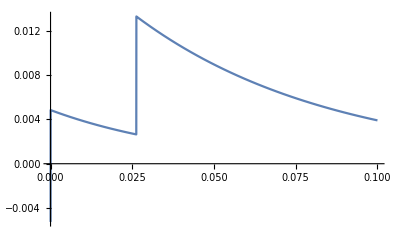

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/7 √(11+6 √2)};
nt={1,0,0};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

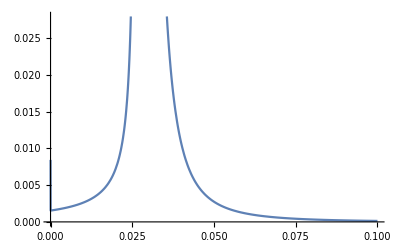

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/12 (14-4 √2+4 √5-4 √10+√(2 (192-115 √2+85 √5-51 √10)))};
nt={1,0,1};
Plot[{totxSec[kt,lt,mt,nt+eps{1,1,1}]},{eps,0,0.1}]
```

-Graphics--Graphics-

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2+1/(√2)-1/2 √(17-12 √2)-√(5/4+1/4 (17-12 Power[«2»])).

0.

-1.35162561193

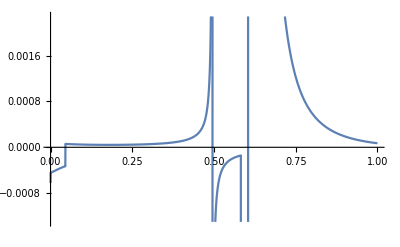

```mathematica
kt={1/2,0,0};
lt={1,-1/2,0};
mt={0,0,1/2 √(17-12 √2)};
nt={1,0,1};
N[myNorm[kt]+myNorm[kt-lt]-myNorm[mt]-myNorm[mt-lt],12]
N[myNorm[kt]+myNorm[kt-lt]-myNorm[lt-nt]-myNorm[mt-nt]-myNorm[mt],12]
Plot[{totxSec[kt,lt,mt+eps{1,1,1},nt]},{eps,0,1}]
```